```mathematica
calcBins[data_,start_,end_,binCount_]:=Block[{ret,idx},
ret=Table[0,{i,1,binCount}];
For[i=1,i<=Length[data],i++,
If[ data[[i]]>=start&&data[[i]]<end,
idx=Floor[((data[[i]]-start)binCount)/(end-start)]+1;
ret[[idx]]=ret[[idx]]+1;
];
];
Return[ret];
];
calcSS[data1_,data2_,data3_,cs1_,cs2_,cs3_,start_,binCount_]:=Block[{b1,b2,b3,minS,ret},
b1=Table[0,{i,1,binCount}];
b2=Table[0,{i,1,binCount}];
b3=Table[0,{i,1,binCount}];
ret=Table[0,{i,1,binCount}];
For[i=1,i<=binCount,i++,
minS=(1-start)/binCount*(i-1)+start;
b1[[i]]=Sum[If[data1[[j]]>=minS,1,0],{j,1,Length[data1]}];
b2[[i]]=Sum[If[data2[[j]]>=minS,1,0],{j,1,Length[data2]}];
b3[[i]]=Sum[If[data3[[j]]>=minS,1,0],{j,1,Length[data3]}];
];
For[i=1,i<=binCount,i++,
If[b3[[i]]>0,ret[[i]]=(b3[[i]]*cs3)/(√(b3[[i]]*cs3+b2[[i]]*cs2+b1[[i]]*cs1))]
];
Return[ret];
];
score[h_,n_]:=2^(-h/(2HarmonicNumber[n-1]-2(n-1)/n));
scorefast[h_,cn_]:=2^(-h/cn);
scorelst[lst_,cn_]:=2^((-Mean[lst])/cn);
calcFrac[data1_,data2_,data3_,start_,end_,binCount_]:=Block[{b1,b2,b3,minS,ret},
b1=Table[0,{i,1,binCount}];
b2=Table[0,{i,1,binCount}];
b3=Table[0,{i,1,binCount}];
ret=Table[{0,0},{i,1,binCount}];
For[i=1,i<=binCount,i++,
minS=(end-start)/binCount*(i-1)+start;
b1[[i]]=Sum[If[data1[[j]]>=minS,1,0],{j,1,Length[data1]}];
b2[[i]]=Sum[If[data2[[j]]>=minS,1,0],{j,1,Length[data2]}];
b3[[i]]=Sum[If[data3[[j]]>=minS,1,0],{j,1,Length[data3]}];
];
For[i=1,i<=binCount,i++,
If[b3[[i]]>0,ret[[i,1]]=N[b3[[i]]/(b1[[i]]+b2[[i]]+b3[[i]])];ret[[i,2]]=N[(b2[[i]]+b3[[i]])/(b1[[i]]+b2[[i]]+b3[[i]])]]
];
Return[ret];
];
```

## V0 Results

## Fast Check

```mathematica
ToDipict=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0.csv","CSV"]];
```

```mathematica
listSM={};
listRR={};
listNP={};
Dynamic[prog]
ProgressIndicator[prog]
prog=0;
cn=N[2HarmonicNumber[Length[ToDipict]-1]-2(Length[ToDipict]-1)/Length[ToDipict]];
For[i=1,i<=Length[ToDipict],i++,
If[Round[ToDipict[[i,1]]]==0,AppendTo[listSM,scorefast[ToDipict[[i,2]],cn]]];
If[Round[ToDipict[[i,1]]]==1,AppendTo[listRR,scorefast[ToDipict[[i,2]],cn]]];
If[Round[ToDipict[[i,1]]]==2,AppendTo[listNP,scorefast[ToDipict[[i,2]],cn]]];
prog=prog+N[1/Length[ToDipict]];
]
```

## Results

```mathematica
HistoryData=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0.csv","CSV"]];
HistoryData2=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0-1.csv","CSV"]];
(*HistoryData3=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0-2.csv","CSV"]];*)
```

```mathematica
(* 2000 is enough *)
```

```mathematica
Length[HistoryData]
Length[HistoryData2]
(*Length[HistoryData3]*)
```

40550

40550

40550

```mathematica
listSM={};
listRR={};
listNP={};
maxl=1001;
ProgressIndicator[Dynamic[prog]]
prog=0;
cn=N[2HarmonicNumber[Length[HistoryData]-1]-2(Length[HistoryData]-1)/Length[HistoryData]];
For[i=1,i<=Length[HistoryData],i++,
If[Round[HistoryData[[i,1]]]==0,AppendTo[listSM,scorelst[{Mean[Take[HistoryData[[i]],{2,maxl}]],Mean[Take[HistoryData2[[i]],{2,maxl}]](*,Mean[Take[HistoryData3[[i]],{2,maxl}]]*)},cn]]];
If[Round[HistoryData[[i,1]]]==1,AppendTo[listRR,scorelst[{Mean[Take[HistoryData[[i]],{2,maxl}]],Mean[Take[HistoryData2[[i]],{2,maxl}]](*,Mean[Take[HistoryData3[[i]],{2,maxl}]]*)},cn]]];
If[Round[HistoryData[[i,1]]]==2,AppendTo[listNP,scorelst[{Mean[Take[HistoryData[[i]],{2,maxl}]],Mean[Take[HistoryData2[[i]],{2,maxl}]](*,Mean[Take[HistoryData3[[i]],{2,maxl}]]*)},cn]]];
prog=prog+N[1/Length[HistoryData]];
]
```

```mathematica
listNP
```

{0.706742,0.766345,0.622321,0.634341,0.555171,0.608608,0.468025,0.562267,0.598126,0.70348,0.491846,0.573153,0.631427,0.457135,0.758693,0.685502,0.69189,0.666522,0.548811,0.75225,0.643579,0.517861,0.729791,0.663431,0.590323,0.616009,0.489532,0.823965,0.624484,0.382041,0.668877,0.683166,0.730619,0.617751,0.53779,0.573348,0.562656,0.603672,0.538492,0.486659,0.508642,0.699305,0.46493,0.667975,0.636871,0.628841,0.67156,0.564119,0.709424,0.689126}

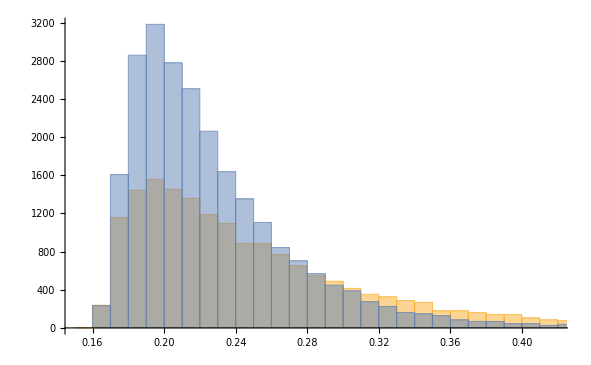

```mathematica
Histogram[{listSM,listRR},50]
```

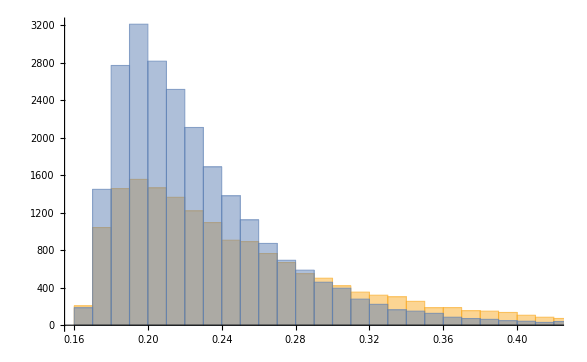

```mathematica
Histogram[{listSM,listRR},50]
```

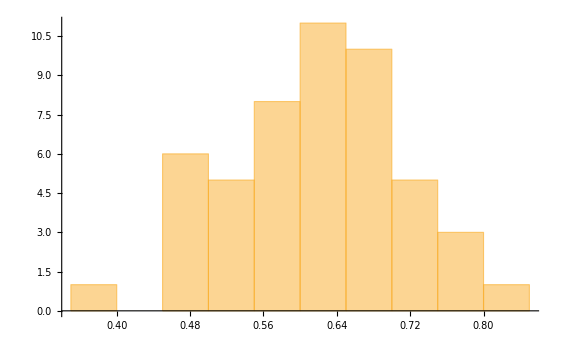

```mathematica
Histogram[{listNP},12]
```

```mathematica
calcBins[listNP,0.15,0.85,35]
calcBins[listSM,0.15,0.85,35]
calcBins[listRR,0.15,0.85,35]
```

{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,1,3,1,3,4,2,4,4,5,5,4,3,1,2,3,0,0,1,0}

{205,2497,3018,2582,2000,1655,1218,921,675,556,373,306,243,158,100,108,81,58,25,18,18,13,8,7,1,1,0,0,0,1,0,0,0,0,0}

{185,4218,6024,4623,3067,1994,1281,854,502,313,214,134,91,69,29,25,14,7,7,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Max[listSM]
```

0.745154

```mathematica
Sum[If[listNP[[n]]>Max[listSM],1,0],{n,1,50}]
```

4

```mathematica
calcSS[listSM,listRR,listNP,306.6/16846,430.5/23654,0.91/50,0.5,500]
```

{0.447557,0.451607,0.45437,0.45577,0.460049,0.464452,0.470523,0.472079,0.472079,0.468929,0.472175,0.472175,0.477171,0.478872,0.480592,0.48233,0.485864,0.489476,0.481428,0.483262,0.490813,0.492757,0.496715,0.49873,0.504926,0.509187,0.515786,0.518043,0.522648,0.522648,0.524997,0.527378,0.529792,0.532239,0.532239,0.53472,0.537236,0.539789,0.539789,0.547669,0.528788,0.528788,0.531479,0.536987,0.539806,0.542669,0.548536,0.551542,0.554598,0.557705,0.546483,0.546483,0.549615,0.556044,0.562703,0.554618,0.561595,0.561595,0.565183,0.572571,0.572571,0.572571,0.576376,0.572362,0.560368,0.564357,0.552191,0.556236,0.564601,0.564601,0.568928,0.568928,0.573355,0.573355,0.560891,0.552739,0.562029,0.571804,0.571804,0.571804,0.571804,0.571804,0.571804,0.576887,0.582108,0.582108,0.587473,0.598664,0.598664,0.604505,0.61052,0.61052,0.597446,0.597446,0.597446,0.610025,0.610025,0.610025,0.610025,0.603323,0.603323,0.617195,0.624499,0.624499,0.624499,0.611,0.61859,0.61859,0.61859,0.61859,0.612776,0.612776,0.612776,0.612776,0.621001,0.621001,0.629567,0.629567,0.615694,0.601546,0.610593,0.610593,0.610593,0.610593,0.610593,0.596211,0.596211,0.60124,0.611882,0.62311,0.62311,0.608522,0.608522,0.593592,0.578295,0.578295,0.578295,0.562602,0.562602,0.562602,0.562602,0.562602,0.575247,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.559345,0.542991,0.526148,0.526148,0.526148,0.540565,0.523517,0.505903,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.487661,0.468722,0.468722,0.468722,0.468722,0.468722,0.448999,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.406761,0.383953,0.383953,0.383953,0.383953,0.383953,0.359753,0.359753,0.359753,0.333879,0.333879,0.333879,0.333879,0.333879,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.305941,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.241329,0.269815,0.269815,0.269815,0.269815,0.269815,0.269815,0.269815,0.233666,0.233666,0.233666,0.233666,0.233666,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.190788,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0.134907,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
0.629
```

```mathematica
0.6257712082262211/(√(0.6257712082262211`+0.29+1.74*0.23*0.23))
```

0.738599

```mathematica
HistoryData[[1,1]]
HistoryData[[16847,1]]
HistoryData[[40501,1]]
```

0.

1.

2.

```mathematica
1/(√2000)StandardDeviation[Join[Take[HistoryData[[1]],{2,1001}],Take[HistoryData2[[1]],{2,1001}]]]/Mean[Join[Take[HistoryData[[1]],{2,1001}],Take[HistoryData2[[1]],{2,1001}]]]//N
1/(√2000)StandardDeviation[Join[Take[HistoryData[[16847]],{2,1001}],Take[HistoryData2[[16847]],{2,1001}]]]/Mean[Join[Take[HistoryData[[16847]],{2,1001}],Take[HistoryData2[[16847]],{2,1001}]]]//N
1/(√2000)StandardDeviation[Join[Take[HistoryData[[40501]],{2,1001}],Take[HistoryData2[[40501]],{2,1001}]]]/Mean[Join[Take[HistoryData[[40501]],{2,1001}],Take[HistoryData2[[40501]],{2,1001}]]]//N
```

0.00626643

0.00470869

0.00978686

```mathematica
AllP=Table[N[1/(√2000)StandardDeviation[Join[Take[HistoryData[[n]],{2,1001}],Take[HistoryData2[[n]],{2,1001}]]]/Mean[Join[Take[HistoryData[[n]],{2,1001}],Take[HistoryData2[[n]],{2,1001}]]]],{n,1,Length[HistoryData]}];
```

```mathematica
Mean[AllP]
```

0.00520438

```mathematica
Max[AllP]
```

0.0136612

```mathematica
Min[AllP]
```

0.00424935

```mathematica
HistoryDataA=Join[Take[HistoryData[[1]],{2,1001}],Take[HistoryData2[[1]],{2,1001}]];
HistoryDataB=Join[Take[HistoryData[[16847]],{2,1001}],Take[HistoryData2[[16847]],{2,1001}]];
HistoryDataC=Join[Take[HistoryData[[40501]],{2,1001}],Take[HistoryData2[[40501]],{2,1001}]];
pt1=Table[Mean[Take[HistoryDataA,{1,n}]],{n,1,2000}]//N
pt2=Table[Mean[Take[HistoryDataB,{1,n}]],{n,1,2000}]//N
pt3=Table[Mean[Take[HistoryDataC,{1,n}]],{n,1,2000}]//N
```

{27.,34.5,30.3333,31.5,31.,29.6667,28.4286,30.,30.6667,30.2,29.,29.8333,30.,29.9286,28.9333,29.25,29.1176,28.6667,28.5789,28.3,28.2857,29.1818,29.3478,30.,29.8,29.6538,30.0741,30.0357,30.2759,29.9,30.3548,30.0313,29.7879,29.6471,29.9429,29.8611,29.7568,29.3947,29.8462,29.725,30.0976,30.3333,30.2791,29.9318,29.9778,30.1522,29.9574,30.0208,30.3469,30.5,30.549,30.6923,30.6038,30.8519,30.8727,30.6964,30.5088,30.4483,30.3729,30.3,30.1639,30.2097,30.2222,30.0938,30.2,30.197,30.1642,30.1765,30.3478,30.3286,30.2113,30.1528,29.9726,29.9595,30.1467,30.0658,30.1948,30.2949,30.2658,30.45,30.4568,30.4634,30.4819,30.6667,30.5765,30.6163,30.5747,30.6477,30.6966,30.6444,30.6044,30.5761,30.5161,30.6277,30.7579,30.5833,30.6907,30.4694,30.5556,30.78,30.7723,30.6471,30.6311,30.625,30.619,30.6981,30.8411,30.8426,30.7248,30.7273,30.6937,30.7232,30.7611,30.8333,30.8609,30.819,30.8034,30.7373,30.7311,30.6417,30.6198,30.5082,30.4959,30.4839,30.472,30.5635,30.4882,30.5234,30.4729,30.5077,30.5496,30.5682,30.5564,30.5373,30.5778,30.5515,30.5328,30.529,30.5252,30.4786,30.5532,30.4507,30.4056,30.3958,30.4207,30.4315,30.3265,30.2838,30.2752,30.18,30.106,30.0855,30.1111,30.2208,30.1742,30.1346,30.1146,30.1076,30.0063,29.9938,30.0186,30.,29.9816,30.0427,30.0061,30.,29.976,29.9643,30.0178,30.0059,30.0643,30.0116,30.0231,30.069,30.0114,29.9489,29.9435,30.0562,29.9944,29.9944,30.0055,29.978,30.0273,30.0163,30.0162,30.0753,30.1283,30.0904,30.0265,30.0368,30.0157,29.9583,29.9585,29.9485,29.9487,29.9337,29.9645,29.9848,29.9698,29.99,30.0249,29.9851,30.0197,30.0833,30.1073,30.0825,30.0676,30.0385,29.9665,30.0381,30.0427,30.1462,30.1502,30.1636,30.1907,30.1852,30.212,30.1697,30.137,30.1591,30.1403,30.1441,30.1345,30.0759,30.1244,30.1283,30.1101,30.0658,30.0873,30.087,30.0736,30.0603,30.0472,30.0256,30.0255,29.9534,29.962,29.9832,29.9833,29.9917,30.,29.9959,29.9465,29.9836,29.9959,29.9472,29.9271,29.9718,30.,29.96,29.9004,29.9008,29.8814,29.9173,29.9412,29.957,29.93,29.9341,29.9305,29.8962,29.9272,29.9466,29.9696,29.947,29.9925,29.9624,29.985,29.9813,29.9591,29.9333,29.9668,29.9632,29.9414,29.8978,29.9018,29.9022,29.9278,29.9065,29.9319,29.9321,29.9039,29.8901,29.9435,29.9296,29.9649,29.8986,29.8676,29.9306,29.9827,29.9621,29.9794,29.9521,29.9386,29.9014,29.8983,29.9324,29.9125,29.906,29.9331,29.92,29.907,29.9371,29.9307,29.9507,29.9738,29.9902,29.9642,29.9286,29.9094,29.929,29.9357,29.9583,29.9553,29.949,29.9651,29.9399,29.9306,29.8962,29.8934,29.8813,29.8536,29.8634,29.8576,29.8426,29.8615,29.8865,29.896,29.8415,29.8024,29.8394,29.8489,29.8886,29.8979,29.8952,29.9045,29.8869,29.8487,29.8817,29.8938,29.8765,29.8387,29.7924,29.8309,29.8634,29.8493,29.8121,29.8069,29.7989,29.8309,29.8314,29.8177,29.8494,29.8385,29.8418,29.8254,29.7865,29.7927,29.8352,29.8273,29.8194,29.8532,29.8425,29.8292,29.7885,29.7836,29.7787,29.7575,29.7745,29.7561,29.7622,29.8005,29.7903,29.7962,29.7834,29.8,29.8644,29.8594,29.836,29.8443,29.8395,29.8451,29.8246,29.8146,29.8073,29.774,29.8057,29.814,29.7835,29.7686,29.7692,29.7801,29.7806,29.771,29.7817,29.7848,29.7879,29.7783,29.7563,29.7619,29.7825,29.7731,29.7687,29.7667,29.7896,29.758,29.7562,29.7371,29.7353,29.7531,29.722,29.7056,29.7087,29.6804,29.6763,29.6675,29.6659,29.6906,29.677,29.7088,29.6929,29.7007,29.6967,29.6903,29.6792,29.6753,29.6831,29.7026,29.6986,29.7016,29.7,29.6868,29.6898,29.7044,29.6912,29.7103,29.6789,29.659,29.653,29.656,29.6477,29.6712,29.69,29.6975,29.6757,29.6584,29.657,29.6376,29.6228,29.6169,29.6022,29.5765,29.5996,29.5872,29.5705,29.5934,29.5877,29.5536,29.5284,29.5185,29.513,29.5315,29.5152,29.5011,29.5086,29.5183,29.515,29.546,29.5705,29.6247,29.6064,29.5987,29.5763,29.5603,29.557,29.5874,29.5945,29.6101,29.5816,29.5595,29.5417,29.5489,29.556,29.5652,29.5785,29.5794,29.5926,29.6037,29.6004,29.6155,29.6061,29.6029,29.6016,29.5943,29.5951,29.5859,29.5706,29.5694,29.5643,29.5571,29.552,29.5449,29.5359,29.5388,29.5456,29.5386,29.5119,29.501,29.4961,29.499,29.4824,29.4736,29.4863,29.4834,29.5,29.5068,29.5233,29.5048,29.4961,29.499,29.5115,29.4971,29.4732,29.4761,29.4752,29.4571,29.4772,29.4516,29.4261,29.4423,29.4528,29.4539,29.453,29.4578,29.4569,29.4785,29.4776,29.4693,29.4461,29.4601,29.45,29.4566,29.4649,29.4604,29.4816,29.4899,29.478,29.479,29.4708,29.4463,29.4527,29.4392,29.4348,29.4322,29.4549,29.4559,29.446,29.4578,29.4695,29.4723,29.4696,29.492,29.5053,29.492,29.4823,29.4726,29.5265,29.5291,29.5352,29.536,29.5368,29.5534,29.5664,29.5567,29.5296,29.5287,29.533,29.5477,29.5329,29.5492,29.55,29.5422,29.5344,29.5163,29.5257,29.5333,29.5273,29.5315,29.5238,29.5348,29.5475,29.5482,29.5456,29.5464,29.532,29.5277,29.5369,29.5477,29.5184,29.5142,29.5117,29.5408,29.5598,29.5622,29.5662,29.5636,29.5594,29.5502,29.5609,29.5501,29.541,29.5434,29.5408,29.5791,29.5668,29.5854,29.5812,29.5608,29.5663,29.5428,29.5629,29.5684,29.5836,29.5827,29.5609,29.5728,29.5591,29.5662,29.5653,29.5517,29.5444,29.5578,29.5538,29.5577,29.5505,29.5449,29.5629,29.551,29.5439,29.529,29.4984,29.4852,29.4751,29.4728,29.4984,29.4822,29.4721,29.4822,29.466,29.473,29.4892,29.4869,29.4923,29.4747,29.4801,29.4595,29.4588,29.4353,29.421,29.4127,29.4455,29.466,29.4441,29.4389,29.4623,29.4526,29.4685,29.4588,29.4731,29.4918,29.4776,29.465,29.4732,29.4725,29.4718,29.4785,29.4808,29.4815,29.5015,29.5214,29.5265,29.5345,29.5132,29.5183,29.5,29.5387,29.5437,29.5284,29.5218,29.5196,29.5203,29.508,29.4971,29.4921,29.5086,29.505,29.4914,29.4892,29.5086,29.5021,29.4929,29.5036,29.5028,29.495,29.4773,29.4766,29.4618,29.4696,29.4845,29.4965,29.4972,29.4965,29.4888,29.5007,29.507,29.5189,29.5112,29.5258,29.5306,29.516,29.5236,29.5284,29.5263,29.5256,29.518,29.5048,29.5028,29.5048,29.5082,29.5213,29.5384,29.5171,29.5615,29.5525,29.5572,29.5429,29.5543,29.5658,29.5799,29.5683,29.5946,29.587,29.5849,29.5653,29.5618,29.5866,29.5724,29.5703,29.5816,29.5848,29.6027,29.5939,29.5824,29.5843,29.5729,29.5616,29.5582,29.5641,29.558,29.5534,29.55,29.5453,29.5367,29.5518,29.5759,29.5516,29.5535,29.5554,29.5638,29.5501,29.5403,29.5473,29.5518,29.5511,29.5388,29.5484,29.5451,29.5431,29.5566,29.5661,29.5564,29.5608,29.5639,29.5734,29.5638,29.5592,29.5369,29.5197,29.5178,29.5057,29.4899,29.4766,29.4659,29.4716,29.4622,29.4591,29.4611,29.4642,29.4599,29.4393,29.4525,29.4544,29.4526,29.4296,29.4229,29.4236,29.428,29.404,29.4072,29.4141,29.4099,29.4032,29.415,29.4305,29.4263,29.4294,29.4216,29.4259,29.4401,29.4249,29.4207,29.4202,29.41,29.4265,29.432,29.4412,29.4298,29.4305,29.4444,29.4391,29.4458,29.4597,29.4615,29.461,29.4628,29.4743,29.4737,29.4815,29.4797,29.4934,29.4893,29.4935,29.4846,29.4781,29.4739,29.4663,29.4704,29.4628,29.4729,29.4865,29.4847,29.4759,29.4812,29.4818,29.4918,29.4901,29.4813,29.4924,29.4942,29.4994,29.4977,29.4948,29.4954,29.4797,29.4641,29.4636,29.4503,29.4579,29.4447,29.4407,29.4264,29.4225,29.4186,29.4181,29.4222,29.4046,29.4041,29.4059,29.4146,29.4073,29.4,29.4064,29.4127,29.4213,29.4163,29.4215,29.4391,29.4329,29.4685,29.4499,29.4584,29.4444,29.4372,29.4412,29.4374,29.4335,29.442,29.4437,29.431,29.4294,29.4433,29.4517,29.4446,29.4585,29.4524,29.4519,29.4536,29.462,29.4824,29.4686,29.4626,29.4479,29.4287,29.4458,29.4245,29.4404,29.4454,29.4449,29.4553,29.4635,29.4696,29.4723,29.4631,29.4626,29.4481,29.4454,29.4406,29.4509,29.4644,29.4521,29.4462,29.4372,29.4421,29.4502,29.4411,29.4471,29.4444,29.4376,29.4254,29.4058,29.3957,29.3985,29.396,29.4125,29.4195,29.4138,29.4038,29.4013,29.3871,29.3836,29.3716,29.3733,29.3824,29.3725,29.3878,29.3885,29.4027,29.4065,29.4113,29.4108,29.4031,29.3985,29.4012,29.405,29.4004,29.3927,29.4172,29.4105,29.4081,29.4138,29.4144,29.4027,29.394,29.3895,29.4025,29.4,29.3934,29.3961,29.4039,29.3922,29.3867,29.3914,29.39,29.3917,29.3821,29.398,29.3884,29.3901,29.3947,29.3893,29.3808,29.3764,29.376,29.3948,29.3944,29.396,29.3865,29.3962,29.3858,29.3974,29.411,29.4136,29.4042,29.4088,29.4094,29.4328,29.4314,29.4409,29.4573,29.4549,29.4564,29.4609,29.4802,29.4798,29.4862,29.4828,29.4715,29.4612,29.4578,29.4495,29.4657,29.4809,29.4804,29.479,29.4697,29.4839,29.4873,29.4761,29.4835,29.4898,29.4854,29.483,29.4748,29.4705,29.4681,29.4647,29.4759,29.4812,29.4788,29.4764,29.4644,29.4707,29.475,29.4631,29.4464,29.4392,29.4436,29.4355,29.4332,29.4366,29.4286,29.4225,29.4135,29.416,29.4108,29.4133,29.4148,29.4078,29.4112,29.4325,29.4274,29.4373,29.4237,29.4374,29.4286,29.4413,29.4306,29.4208,29.4045,29.4079,29.4075,29.3922,29.3862,29.3737,29.3855,29.3842,29.3801,29.3807,29.3831,29.3698,29.3639,29.3562,29.3651,29.3721,29.369,29.3733,29.3785,29.3827,29.3768,29.3737,29.3725,29.3776,29.3736,29.3632,29.3629,29.3671,29.3659,29.3719,29.3761,29.3758,29.3845,29.3833,29.3984,29.3917,29.3822,29.381,29.3743,29.3749,29.3718,29.3634,29.3613,29.3627,29.357,29.3603,29.3609,29.365,29.362,29.3662,29.3703,29.3735,29.3723,29.3764,29.3859,29.3874,29.3897,29.3876,29.3854,29.394,29.4016,29.3871,29.3867,29.3882,29.3922,29.3804,29.3827,29.3762,29.3864,29.3852,29.377,29.3723,29.3702,29.3734,29.3722,29.3736,29.382,29.3799,29.37,29.374,29.372,29.3768,29.373,29.3727,29.3785,29.3833,29.3744,29.3671,29.3798,29.3673,29.3731,29.3676,29.3664,29.3704,29.3718,29.3801,29.3832,29.3725,29.3688,29.3702,29.3733,29.3687,29.3581,29.3629,29.3729,29.3674,29.3629,29.3651,29.3835,29.3789,29.3769,29.3766,29.372,29.3743,29.3926,29.3914,29.3868,29.4008,29.4005,29.4052,29.4209,29.4121,29.4286,29.4341,29.4421,29.4325,29.4271,29.4285,29.4281,29.4269,29.4299,29.4312,29.4333,29.4296,29.4343,29.4289,29.4302,29.4257,29.4279,29.4159,29.4321,29.4359,29.4496,29.4509,29.4645,29.4617,29.4563,29.4568,29.4515,29.4454,29.4442,29.4471,29.4459,29.4505,29.4468,29.4473,29.4436,29.4449,29.4388,29.4458,29.4479,29.4508,29.4585,29.4574,29.4562,29.4639,29.4603,29.4607,29.4466,29.4414,29.4475,29.4439,29.454,29.4488,29.4589,29.4602,29.4558,29.4466,29.439,29.4346,29.4359,29.4299,29.432,29.4261,29.4161,29.4246,29.4314,29.4279,29.4355,29.4399,29.4523,29.4567,29.454,29.4552,29.4572,29.4632,29.4636,29.468,29.4692,29.4672,29.4669,29.4712,29.474,29.4815,29.4796,29.4815,29.471,29.458,29.4491,29.4495,29.4452,29.4394,29.4469,29.4543,29.4618,29.4497,29.4369,29.435,29.4316,29.4336,29.4325,29.4228,29.4171,29.4152,29.4234,29.4285,29.4274,29.4286,29.4205,29.4202,29.4214,29.418,29.4208,29.432,29.4339,29.4459,29.4387,29.4429,29.4372,29.4491,29.4365,29.4316,29.426,29.4348,29.4375,29.4379,29.4368,29.4411,29.4422,29.4503,29.4446,29.4556,29.4682,29.4572,29.4675,29.4717,29.4736,29.4687,29.4804,29.4732,29.4729,29.474,29.4767,29.4853,29.4857,29.4929,29.4948,29.4876,29.4918,29.4914,29.4858,29.4839,29.4813,29.4899,29.4903,29.4974,29.5015,29.5026,29.497,29.5026,29.5082,29.5056,29.5044,29.51,29.5148,29.5137,29.5059,29.5129,29.5199,29.5203,29.5177,29.5055,29.5044,29.5026,29.5029,29.4989,29.4927,29.4894,29.4846,29.4901,29.4949,29.4865,29.492,29.4953,29.5015,29.5047,29.4971,29.5004,29.4906,29.4829,29.4775,29.4822,29.471,29.4757,29.4732,29.4743,29.4718,29.465,29.469,29.473,29.4661,29.4572,29.4647,29.4694,29.4749,29.476,29.467,29.4652,29.4585,29.4538,29.4535,29.4603,29.4571,29.454,29.4486,29.4426,29.4416,29.4505,29.4495,29.4584,29.4581,29.4656,29.4631,29.4522,29.4533,29.4501,29.4491,29.4445,29.4442,29.4382,29.4408,29.4383,29.4521,29.4504,29.4522,29.4469,29.448,29.4449,29.4369,29.4324,29.4258,29.4213,29.4203,29.4221,29.4162,29.4096,29.4079,29.4111,29.4199,29.4259,29.4152,29.4142,29.4243,29.4247,29.4182,29.4179,29.4127,29.4042,29.4004,29.4008,29.4006,29.401,29.3931,29.3963,29.3994,29.4074,29.412,29.4165,29.4224,29.4283,29.4211,29.4154,29.4171,29.4155,29.4179,29.4163,29.4139,29.415,29.4154,29.4083,29.4237,29.4289,29.4286,29.4249,29.4341,29.4325,29.4342,29.4373,29.4329,29.4292,29.4249,29.4185,29.4182,29.4112,29.4089,29.4107,29.4036,29.4054,29.4179,29.4102,29.4073,29.4103,29.4034,29.4064,29.4102,29.4059,29.405,29.4161,29.4111,29.4048,29.4079,29.4023,29.4007,29.4017,29.4028,29.4079,29.4063,29.4066,29.409,29.4054,29.4005,29.4003,29.3967,29.3865,29.3902,29.3893,29.3877,29.3888,29.3918,29.3916,29.39,29.3851,29.3829,29.3964,29.3922,29.3946,29.3963,29.4033,29.4004,29.3975,29.3986,29.3937,29.3941,29.405,29.3956,29.3907,29.3879,29.3831,29.3952,29.4001,29.3914,29.3925,29.3968,29.3997,29.4008,29.3947,29.388,29.3877,29.3894,29.384,29.3882,29.3796,29.3858,29.3907,29.3879,29.3838,29.3867,29.3826,29.3798,29.3764,29.3787,29.3746,29.3769,29.3799,29.3771,29.3756,29.3696,29.3668,29.3685,29.372,29.3712,29.3633,29.3694,29.3717,29.3683,29.3636,29.3628,29.3676,29.3629,29.3583,29.3606,29.3534,29.3582,29.3504,29.3451,29.3468,29.3504,29.3508,29.3537,29.3516,29.3514,29.3575,29.3509,29.3488,29.3411,29.3421,29.3419,29.3448,29.3434,29.3444,29.3398,29.3415,29.3406,29.3442,29.3402,29.3444,29.3441,29.3402,29.335,29.3354,29.3284,29.3275,29.3286,29.3222,29.3182,29.3224,29.3247,29.3257,29.328,29.3216,29.322,29.3175,29.3278,29.3251,29.3268,29.3241,29.3251,29.3182,29.3235,29.3264,29.3268,29.3229,29.3202,29.3176,29.3094,29.3135,29.3213,29.3254,29.3191,29.3238,29.3156,29.3191,29.3177,29.3151,29.3203,29.3159,29.3133,29.3198,29.3129,29.3078,29.301,29.2996,29.3115,29.3101,29.3057,29.3073,29.3041,29.2961,29.3013,29.2939,29.2973,29.3008,29.3072,29.3082,29.3087,29.3103,29.3053,29.3063,29.2995,29.2957,29.3052,29.2996,29.2982,29.3016,29.3026,29.3066,29.3148,29.3128,29.3186,29.3196,29.3153,29.3157,29.3167,29.3165,29.3151,29.3209,29.323,29.3282,29.328,29.3219,29.3181,29.3191,29.3343,29.3371,29.3404,29.3438,29.343,29.3493,29.3502,29.3506,29.3451,29.3402,29.3465,29.3539,29.3602,29.3564,29.3509,29.3566,29.3535,29.3503,29.3536,29.3599,29.3591,29.3542,29.3505,29.352,29.3559,29.3551,29.3537,29.3483,29.3481,29.3409,29.3401,29.3417,29.3426,29.3488,29.348,29.3565,29.3546,29.3602,29.3605,29.365,29.3665,29.3564,29.3637,29.3624,29.3581,29.3533,29.3508,29.3443,29.3423,29.3456,29.3437,29.3446,29.3519,29.3448,29.3503,29.3587,29.3625,29.3572,29.361,29.3573,29.3623,29.3661,29.3682,29.3714,29.3694,29.3778,29.3724,29.3768,29.3811,29.3803,29.3852,29.3878,29.3927,29.3936,29.3946,29.396,29.3998,29.4092,29.4027,29.4002,29.3989,29.3998,29.399,29.3948,29.3912,29.3865,29.3874,29.3799,29.3836,29.3884,29.3876,29.3919,29.3883,29.3859,29.3896,29.3888,29.3863,29.3934,29.3993,29.4075,29.4196,29.4149,29.4208,29.4222,29.4192,29.4312,29.4298,29.4246,29.4271,29.4225,29.4294,29.4336,29.4356,29.447,29.4473,29.4393,29.4336,29.4322,29.4331,29.4345,29.4459,29.4351,29.4382,29.4308,29.4305,29.4397,29.4339,29.4337,29.4307,29.4305,29.4291,29.436,29.4435,29.441,29.438,29.4395,29.443,29.4472,29.4497,29.444,29.4426,29.4468,29.4481,29.4446,29.4471,29.4447,29.4461,29.4502,29.457,29.4649,29.4739,29.4688,29.4663,29.4585,29.4702,29.4715,29.4648,29.4624,29.4545,29.4559,29.4589,29.4587,29.4606,29.4657,29.4703,29.4625,29.4564,29.461,29.4607,29.4615,29.4591,29.46,29.4678,29.475,29.4748,29.4692,29.462,29.4558,29.4529,29.4521,29.4519,29.4532,29.4535,29.4522,29.4568,29.4619,29.4643,29.456,29.4601,29.4556,29.4479,29.4514,29.4543,29.4551,29.4559,29.4541,29.4528,29.4531,29.4502,29.4457,29.445,29.45,29.4561,29.458,29.462,29.4623,29.4652,29.4686,29.4605,29.4555,29.4526,29.4482,29.449,29.4461,29.447,29.4388,29.4391,29.4358,29.4371,29.4432,29.4471,29.4579,29.4566,29.4558,29.4608,29.4674,29.4656,29.4737,29.4828,29.4831,29.4802,29.4763,29.4781,29.4784,29.4839,29.479,29.4772,29.4779,29.4767,29.4712,29.4736,29.4816,29.4798,29.4796,29.4747,29.476,29.47,29.4672,29.4685,29.4647,29.4665,29.459,29.4614,29.472,29.4707,29.4725,29.4692,29.4612,29.461,29.4561,29.4538,29.4664,29.4672,29.4721,29.4744,29.4731,29.478,29.4798,29.474,29.4696,29.474,29.4656,29.4628,29.4615,29.4552,29.4585,29.4568,29.4611,29.4588,29.4571,29.4508,29.451,29.4447,29.4379,29.4438,29.44,29.4347,29.4315,29.4343,29.4361,29.4374,29.4407,29.443,29.4473,29.4461,29.4479,29.4491,29.4519,29.4547,29.4545,29.4558,29.4555,29.4518,29.4496,29.4529,29.4551,29.4494,29.4482,29.4429,29.4407,29.436}

{47.,52.5,54.6667,49.5,50.2,51.1667,52.8571,50.375,48.7778,48.2,47.2727,47.5833,47.3077,46.7143,45.3333,45.875,46.4706,46.4444,45.2105,45.35,45.2857,45.5909,45.7826,46.125,46.12,46.5,46.4074,46.1429,46.1379,46.7,46.8387,47.1563,47.2424,47.5882,47.3714,47.1111,47.,46.9737,47.1795,46.825,46.3902,46.0952,46.0465,46.2045,46.5556,46.7174,46.5957,46.4583,46.551,46.98,47.098,47.4808,47.6415,47.5,47.8182,47.7143,47.8421,47.5517,47.4915,47.4667,47.2787,47.4032,47.3333,47.3906,47.3846,47.3485,47.5373,47.3088,47.5072,47.6857,47.5634,47.7639,47.8904,47.9459,48.0133,48.1184,48.2078,48.2949,48.3797,48.225,48.2716,48.1951,48.1325,48.4762,48.4588,48.3605,48.5172,48.625,48.618,48.5,48.6044,48.7935,48.7957,49.,49.0105,48.7917,48.5876,48.6429,48.6566,48.85,48.901,48.8431,48.7184,48.6346,48.6381,48.5283,48.5888,48.5185,48.3028,48.3273,48.2252,48.1339,48.1416,48.2193,48.1739,48.25,48.3419,48.322,48.2689,48.2333,48.2562,48.1148,48.1301,48.121,48.112,48.0873,48.0866,48.1406,48.1938,48.1077,48.0687,48.0985,48.0075,48.0149,47.9481,48.0368,48.1022,48.087,48.0719,47.9071,47.9291,47.8732,47.8531,47.8681,47.8621,47.9178,47.8912,47.8243,47.8456,47.8533,47.8477,47.875,47.8039,47.6948,47.6258,47.5385,47.6561,47.6266,47.4969,47.4688,47.5714,47.5617,47.5767,47.5061,47.4545,47.4036,47.479,47.4881,47.3964,47.3647,47.3743,47.2791,47.2601,47.2701,47.2114,47.3466,47.3672,47.4326,47.4022,47.4278,47.4088,47.456,47.4426,47.3696,47.3459,47.3978,47.4652,47.5213,47.455,47.5105,47.5026,47.4688,47.5337,47.5619,47.5897,47.4847,47.5381,47.5455,47.4975,47.515,47.4279,47.3663,47.4138,47.3186,47.3415,47.3447,47.3768,47.3269,47.3541,47.3857,47.3318,47.4292,47.3944,47.4159,47.3767,47.3657,47.4055,47.4128,47.411,47.4227,47.4208,47.3919,47.3587,47.4063,47.4044,47.4469,47.4185,47.5,47.5546,47.5826,47.6061,47.6034,47.5966,47.594,47.5872,47.5763,47.6962,47.6807,47.6904,47.7042,47.6929,47.7355,47.6708,47.709,47.7551,47.8008,47.8462,47.871,47.8755,47.836,47.7291,47.7421,47.7747,47.8307,47.7922,47.8281,47.856,47.8101,47.8263,47.9115,47.9157,47.9695,47.943,47.9886,47.9509,47.9474,47.9888,47.9813,47.9851,48.0148,48.048,48.1103,48.0916,48.0876,48.0727,48.0725,48.0325,48.0504,48.1362,48.1286,48.0854,48.078,48.1767,48.1831,48.1825,48.1573,48.1115,48.0417,48.083,48.0655,48.0687,48.0548,48.0648,48.0884,48.0678,48.0811,48.1347,48.1107,48.1104,48.1233,48.0598,48.0728,48.0924,48.0362,47.9836,48.0163,47.9446,47.9708,47.9353,47.9677,47.9678,47.9487,47.9105,47.8822,47.8952,47.8797,47.8644,47.8302,47.7868,47.7719,47.7788,47.8106,47.8235,47.7623,47.7508,47.7761,47.8043,47.7835,47.7325,47.7091,47.7402,47.747,47.7447,47.7335,47.7552,47.7411,47.7804,47.7722,47.7906,47.8235,47.8592,47.8275,47.8688,47.875,47.942,47.9566,47.9712,47.9598,48.0201,48.0371,48.1254,48.125,48.1048,48.0847,48.0648,48.0646,48.0644,48.1034,48.078,48.1139,48.1247,48.1519,48.1543,48.0934,48.0767,48.0464,48.0381,48.0136,48.0081,48.027,48.0243,48.0296,47.9893,48.0134,48.0053,48.0106,48.0106,47.9974,48.,48.0132,47.9869,47.966,47.9556,47.9271,47.9065,47.9093,47.9406,47.933,47.9383,47.9231,47.9156,47.8903,47.9109,47.8528,47.8532,47.8813,47.8866,47.8693,47.8296,47.8325,47.8105,47.8308,47.8114,47.8416,47.8691,47.8448,47.8403,47.8799,47.8924,47.8976,47.8662,47.8568,47.8717,47.8382,47.8386,47.8149,47.8441,47.8445,47.8878,47.8976,47.905,47.9265,47.9078,47.9434,47.9529,47.9977,47.9836,48.,47.9557,48.007,47.9768,47.9398,47.9423,47.9747,47.9586,47.922,47.9405,47.9543,47.9613,47.9227,47.9524,47.9593,47.9323,47.9189,47.8944,47.9126,47.9329,47.9286,47.9577,47.9689,47.9401,47.927,47.9272,47.9229,47.9121,47.9101,47.9059,47.8777,47.8802,47.8978,47.8894,47.8636,47.933,47.9224,47.9204,47.9056,47.8972,47.9188,47.919,47.9191,47.9193,47.9258,47.8753,47.8713,47.9179,47.9055,47.8973,47.8808,47.8894,47.9375,47.9064,47.9585,47.9441,47.9587,47.9402,47.9239,47.9322,47.9242,47.9202,47.9429,47.9267,47.9228,47.9148,47.8806,47.8626,47.8528,47.8471,47.8193,47.8096,47.834,47.8044,47.7869,47.8052,47.7679,47.7941,47.8004,47.8185,47.8248,47.8035,47.7941,47.771,47.7813,47.7895,47.8016,47.8136,47.8333,47.8511,47.8958,47.921,47.8827,47.8733,47.887,47.9082,47.8874,47.901,47.9411,47.9431,47.9129,47.9168,47.9547,47.9736,47.9549,47.9568,47.9363,47.9103,47.9328,47.9106,47.881,47.8442,47.8278,47.8503,47.8413,47.814,47.8217,47.7927,47.7692,47.8026,47.7956,47.7905,47.7927,47.7985,47.788,47.7975,47.7852,47.8054,47.8399,47.8761,47.8781,47.8891,47.8964,47.8841,47.8843,47.8774,47.8794,47.8637,47.9258,47.9383,47.9225,47.9192,47.9211,47.9545,47.986,47.9599,47.9495,47.9409,47.9323,47.9307,47.9394,47.924,47.9534,47.9329,47.933,47.9348,47.9384,47.9419,47.9317,47.9693,47.9762,47.9474,47.9424,47.9662,47.9493,47.9747,47.968,47.9378,47.9715,47.9631,47.9498,47.9399,47.9217,47.9717,47.9767,47.9818,47.9719,47.9488,47.9208,47.944,47.9786,47.9409,47.9361,47.9362,47.9101,47.925,47.9218,47.9252,47.9302,47.9238,47.9434,47.9467,47.9355,47.9404,47.9405,47.9326,47.9167,47.9104,47.893,47.8979,47.9013,47.9253,47.9444,47.9556,47.9383,47.9415,47.9338,47.9402,47.9465,47.9199,47.9091,47.9077,47.8844,47.8565,47.8614,47.8663,47.8913,47.8589,47.8421,47.8161,47.8287,47.8382,47.8385,47.8218,47.8113,47.8086,47.8211,47.7985,47.8003,47.8356,47.8298,47.824,47.8621,47.8759,47.8565,47.8446,47.8464,47.8722,47.8544,47.8651,47.8578,47.9013,47.8851,47.8718,47.8676,47.8648,47.8472,47.8311,47.818,47.8168,47.8451,47.8483,47.8324,47.8488,47.8372,47.8331,47.8246,47.8482,47.8222,47.7933,47.7834,47.7881,47.7841,47.7742,47.7991,47.7763,47.7795,47.7727,47.7716,47.7762,47.7794,47.7539,47.75,47.7332,47.7208,47.6999,47.6989,47.6979,47.6813,47.669,47.685,47.708,47.7268,47.7243,47.7037,47.6999,47.6891,47.6811,47.6634,47.6987,47.7033,47.7065,47.7042,47.7115,47.6967,47.686,47.6547,47.6676,47.635,47.6369,47.6236,47.6379,47.6589,47.6635,47.6776,47.6767,47.6866,47.6871,47.6875,47.6811,47.6924,47.6874,47.673,47.6653,47.6833,47.6878,47.7003,47.7235,47.7319,47.7416,47.7553,47.7837,47.788,47.7883,47.8005,47.8021,47.7944,47.8026,47.7804,47.7609,47.7493,47.7734,47.7697,47.749,47.7625,47.7628,47.7696,47.766,47.7546,47.7549,47.7396,47.7373,47.726,47.7445,47.7565,47.7775,47.7661,47.7652,47.7693,47.7542,47.7725,47.7908,47.7923,47.7951,47.7992,47.8033,47.7883,47.7669,47.7379,47.7281,47.7348,47.7503,47.7696,47.7649,47.7614,47.7705,47.7695,47.7711,47.7751,47.7616,47.7794,47.7772,47.8,47.8152,47.818,47.8182,47.7886,47.8174,47.8189,47.8278,47.8119,47.8183,47.8185,47.7916,47.8103,47.813,47.8145,47.8233,47.8174,47.8384,47.8509,47.8437,47.8293,47.8234,47.8345,47.8226,47.8519,47.8545,47.8366,47.8343,47.837,47.8432,47.8446,47.8496,47.8594,47.8691,47.8777,47.8838,47.8804,47.8769,47.8926,47.8987,47.906,47.9049,47.9276,47.9371,47.9526,47.9562,47.9598,47.9469,47.9528,47.9647,47.9765,47.973,48.0023,48.0141,48.0059,48.0129,48.028,48.0327,48.0431,48.0384,48.0233,48.0186,48.0174,48.0336,48.0301,48.0324,48.0416,48.0358,48.0357,48.015,48.0138,48.0069,47.9989,47.9989,47.9954,47.9954,47.9783,47.9669,47.9692,47.9716,47.9523,47.958,47.9558,47.9411,47.9423,47.9469,47.9492,47.9459,47.9482,47.9381,47.9483,47.9484,47.954,47.9496,47.9553,47.9419,47.942,47.9242,47.9332,47.9266,47.9344,47.9334,47.9224,47.9402,47.9347,47.9381,47.9404,47.9361,47.935,47.9285,47.9473,47.9561,47.9638,47.9737,47.9694,47.9814,47.9934,48.0098,48.0054,48.0076,48.0109,47.9957,47.9859,47.9816,47.9643,47.9438,47.9341,47.932,47.9235,47.9311,47.914,47.9162,47.9185,47.9143,47.9058,47.9102,47.906,47.9007,47.9083,47.8903,47.8915,47.8831,47.8684,47.8727,47.8814,47.8698,47.8837,47.8817,47.8787,47.8788,47.8642,47.8623,47.8582,47.8562,47.8574,47.8503,47.8598,47.8683,47.8727,47.8613,47.8563,47.8543,47.8576,47.8494,47.86,47.8591,47.8561,47.849,47.8481,47.8566,47.8588,47.8363,47.8333,47.8284,47.8142,47.8174,47.832,47.8301,47.8333,47.8427,47.8327,47.8389,47.8299,47.8321,47.8293,47.8294,47.8327,47.8257,47.8279,47.8119,47.8212,47.8305,47.8558,47.856,47.8592,47.8663,47.8685,47.8706,47.8918,47.8889,47.897,47.9271,47.9112,47.9232,47.9353,47.9264,47.9245,47.9275,47.9276,47.9296,47.9376,47.9337,47.918,47.9161,47.927,47.9212,47.9154,47.9154,47.9155,47.9136,47.9186,47.9167,47.9237,47.9277,47.9297,47.9288,47.9357,47.927,47.9339,47.931,47.9291,47.9447,47.9632,47.9622,47.9778,47.9855,47.9932,47.9884,47.9865,47.9923,47.9913,47.9866,47.9885,47.9712,47.9646,47.9589,47.9618,47.9456,47.9456,47.9409,47.9467,47.9458,47.9382,47.9468,47.944,47.9517,47.9375,47.9281,47.9376,47.9301,47.9245,47.9227,47.9068,47.921,47.9342,47.9437,47.9465,47.9578,47.9429,47.9401,47.9514,47.9496,47.9534,47.9534,47.9637,47.96,47.96,47.9777,47.9852,47.9703,47.975,47.9852,47.9824,47.9852,47.988,48.0065,48.0175,48.0138,48.0221,48.0275,48.0147,48.0266,48.0348,48.0421,48.0539,48.0703,48.062,48.0647,48.071,48.0792,48.0745,48.0636,48.0635,48.0716,48.0643,48.0688,48.0633,48.0623,48.0659,48.0631,48.0604,48.0603,48.0612,48.0611,48.0557,48.0628,48.0663,48.06,48.0662,48.0742,48.0777,48.0946,48.0998,48.1104,48.1192,48.1307,48.1261,48.1242,48.1161,48.1196,48.1257,48.1238,48.1299,48.143,48.1429,48.1401,48.1452,48.1451,48.138,48.1308,48.1281,48.1306,48.1313,48.1304,48.1294,48.117,48.1065,48.1264,48.1341,48.1384,48.1348,48.1173,48.1215,48.1171,48.1187,48.0961,48.1029,48.0968,48.101,48.1079,48.106,48.1034,48.1041,48.1058,48.1005,48.1142,48.1192,48.0968,48.1036,48.1121,48.1111,48.1161,48.1186,48.1194,48.1167,48.1166,48.1327,48.1317,48.1316,48.1255,48.139,48.1363,48.1455,48.1437,48.1351,48.1291,48.1349,48.1449,48.133,48.1421,48.1429,48.1369,48.1443,48.145,48.1558,48.1548,48.1405,48.1387,48.1486,48.1376,48.1267,48.1232,48.1281,48.1255,48.1246,48.1162,48.1285,48.116,48.1167,48.1191,48.1248,48.1329,48.1378,48.1327,48.1334,48.1276,48.1151,48.1265,48.1273,48.1263,48.1361,48.1368,48.1375,48.1447,48.1422,48.1363,48.1362,48.1394,48.1352,48.1229,48.1122,48.1154,48.1112,48.103,48.0964,48.0988,48.1068,48.1043,48.1026,48.1082,48.1145,48.1201,48.1176,48.1215,48.127,48.1398,48.1404,48.1323,48.1218,48.1297,48.1328,48.1319,48.111,48.1197,48.1332,48.1315,48.1202,48.1138,48.1208,48.1144,48.1071,48.1031,48.1078,48.1108,48.1297,48.1273,48.1169,48.1152,48.1167,48.1111,48.1157,48.1227,48.1187,48.121,48.1185,48.1231,48.1238,48.1159,48.1228,48.1157,48.1055,48.1023,48.103,48.0873,48.0849,48.0825,48.0949,48.0932,48.0955,48.0946,48.0907,48.0937,48.0789,48.0727,48.0711,48.0664,48.0556,48.0594,48.0593,48.0631,48.0577,48.073,48.063,48.0675,48.0782,48.0644,48.0613,48.0956,48.0956,48.094,48.0878,48.0847,48.0762,48.0685,48.0738,48.0844,48.0889,48.0812,48.0706,48.0735,48.0705,48.0606,48.0537,48.0506,48.0423,48.0408,48.0452,48.043,48.0361,48.0278,48.0301,48.0443,48.0518,48.0578,48.054,48.0509,48.0524,48.0509,48.0433,48.0418,48.0396,48.0403,48.0268,48.0357,48.035,48.032,48.0319,48.029,48.0393,48.0348,48.0341,48.0444,48.037,48.0355,48.0428,48.0399,48.0391,48.0398,48.0457,48.0427,48.039,48.0367,48.0352,48.0279,48.0264,48.0278,48.0264,48.0271,48.0241,48.0146,47.9985,48.0088,48.0087,48.0102,48.0073,48.0095,48.0094,48.0058,48.0044,48.0094,48.0152,48.0014,48.0043,48.0145,48.0145,48.0318,48.0296,48.0296,48.0202,48.0122,48.0194,48.0273,48.0237,48.0158,48.0151,48.0179,48.0315,48.0372,48.0465,48.0529,48.0536,48.0514,48.0478,48.0485,48.0613,48.0669,48.0733,48.0682,48.0632,48.0752,48.073,48.0617,48.0531,48.0439,48.0396,48.0367,48.0388,48.0289,48.0205,48.0282,48.0394,48.0479,48.0577,48.0471,48.0379,48.0351,48.0245,48.0287,48.0245,48.0273,48.0385,48.0398,48.0524,48.0677,48.0551,48.0523,48.0557,48.0515,48.0382,48.0375,48.0438,48.0389,48.034,48.0305,48.027,48.0256,48.0353,48.038,48.0338,48.029,48.0269,48.0186,48.0145,48.0138,48.0138,48.0117,48.0021,48.0075,48.011,48.,47.9959,47.9973,48.0014,48.0062,47.998,48.0048,48.0034,47.9925,47.9911,48.0048,48.0054,48.0088,48.0122,48.0095,48.0115,48.0129,48.0047,47.9973,47.9926,47.9905,47.9973,47.9959,47.9879,47.9751,47.9737,47.9731,47.9872,47.9738,47.9745,47.9678,47.9584,47.9544,47.945,47.9464,47.9545,47.9452,47.9552,47.9526,47.9466,47.95,47.9467,47.9374,47.9354,47.9388,47.9315,47.9256,47.9276,47.9257,47.9158,47.9099,47.9119,47.9073,47.9114,47.9266,47.9254,47.9188,47.9195,47.9321,47.9321,47.9375,47.9382,47.95,47.9547,47.9593,47.9587,47.9502,47.9482,47.9489,47.9404,47.9333,47.9386,47.9549,47.9452,47.9465,47.9368,47.9309,47.9421,47.9493,47.935,47.9389,47.9383,47.9442,47.9475,47.9475,47.9417,47.9405,47.9373,47.9244,47.9205,47.9187,47.9077,47.9065,47.9053,47.895,47.9118,47.9235,47.9274,47.9261,47.9281,47.9269,47.9256,47.9276,47.9366,47.9258,47.9201,47.9157,47.9227,47.9292,47.9216,47.9178,47.9115,47.9147,47.9097,47.9059,47.8977,47.8933,47.8877,47.889,47.8872,47.8771,47.8747,47.8748,47.8698,47.8692,47.8693,47.8789,47.8815,47.8853,47.8816,47.8829,47.8881,47.8969,47.902,47.9002,47.9103,47.8978,47.906,47.9173,47.913,47.9106,47.9425,47.9507,47.9407,47.9451,47.942,47.9483,47.9458,47.9521,47.9527,47.9484,47.9484,47.9448,47.9435,47.9566,47.9449,47.9387,47.9251,47.9252,47.932,47.9432,47.9506,47.9537,47.9568,47.9575,47.9587,47.9575,47.9545,47.9644,47.9748,47.9687,47.9718,47.9565,47.9547,47.962,47.9608,47.9645,47.9664,47.9701,47.964,47.9677,47.9677,47.9726,47.9744,47.9744,47.9909,47.9982,48.0012,48.0006,48.0061,48.0097,48.0091,48.0067,48.0097,48.0103,48.006,48.0048,48.0036,47.9964,47.9934,48.003,47.9988,47.9934,47.994,47.991,47.9952,47.9988,48.,48.0006,48.003,48.0006,48.003,48.0048,48.0012,48.0006,48.0006,47.9988,48.0078,48.0161,48.0113,48.003,48.0018,48.0054,48.0048,48.0172,48.0238,48.0338,48.0326,48.0314,48.032,48.0332,48.0396,48.0361,48.0455,48.0419,48.0396,48.0348,48.0348,48.0295,48.0271,48.0283,48.0235,48.0182,48.0159,48.0188,48.0106,48.017,48.0229,48.0211,48.0199,48.0199,48.0269,48.0263,48.0386,48.035,48.0368,48.0338,48.0408,48.0437,48.0402,48.039,48.0384,48.0453,48.0401,48.0546,48.0551,48.0557,48.0516,48.0579,48.0463,48.0434,48.0376,48.0352,48.0387,48.0364,48.0334,48.0334,48.038,48.0374,48.027,48.0293,48.0305,48.0293,48.0419,48.0396,48.0442,48.0418,48.0344,48.0286,48.0326,48.032,48.0246,48.032,48.0388,48.0445,48.0376,48.0393,48.0416,48.0427,48.0438,48.0449,48.0511,48.0642,48.0653,48.076,48.0788,48.0703,48.0629,48.0617,48.0617,48.0588,48.0667,48.0621,48.0615,48.0626,48.066,48.0552,48.0574,48.0585,48.0607,48.0585,48.0534,48.0567,48.0516,48.0477,48.0387,48.0359,48.0347,48.0252,48.0257,48.038,48.0413,48.0391,48.0463,48.0402,48.0318,48.039,48.0379,48.0323,48.0323,48.0272,48.0378,48.0333,48.0316,48.0349,48.0316,48.0266,48.0266,48.0238,48.0183,48.0166,48.011,48.0072,48.0061,48.0033,48.0033,48.0099,48.0077,48.0149,48.0176,48.0115,48.0209,48.0159,48.0263,48.023,48.0296,48.0378,48.0367,48.029,48.0377,48.0361,48.0333,48.0377,48.0388,48.0262,48.0229,48.0207,48.012,48.012,48.0114,48.0131,48.0136,48.0071,48.0054,48.0065,48.0043,48.0027,48.0135,48.0179,48.0103,48.0059,48.0005,47.9995,48.0086,48.0103,48.0205,48.0124,48.0054,47.9903,47.9887,47.9898,47.9898,47.9871,47.9919,47.9957,47.993,47.9914,47.9984,47.9946,47.9904,47.9941,47.9925,47.992,47.9915,47.9973,48.0021,48.0011,48.0064,48.0043,48.0027,47.9968,47.9926,48.,48.0027,48.0037,48.0027,48.0053,48.0101,48.027,48.0339,48.0344,48.0407,48.0428,48.046,48.037,48.0348,48.0296,48.0301,48.03,48.0321,48.0342,48.0368,48.0489,48.0547,48.0541,48.0494,48.0415,48.0425,48.0399,48.0367,48.033,48.0304,48.0403,48.045,48.0476,48.0533,48.0512,48.0527,48.0563,48.061,48.0631,48.062,48.0661,48.0708,48.0697,48.0655,48.0779,48.0722,48.0695,48.0669,48.0622,48.0611,48.0518,48.0569,48.0533,48.0465,48.0594,48.0677,48.063,48.066,48.0722,48.0758,48.0757,48.0726,48.0798,48.0813,48.0828,48.0827,48.0745,48.0672,48.0575,48.0631,48.0671,48.0727,48.0686,48.0752,48.0757,48.0772,48.072,48.0827,48.0842,48.0847,48.078,48.0754,48.0744,48.0692,48.0646,48.0692,48.0757,48.0772,48.0797,48.0741,48.0695,48.0735,48.0664,48.0689,48.0689,48.0678,48.0683,48.0617,48.0662,48.0581,48.0581,48.0641,48.0696,48.0655,48.0655,48.0765,48.0715,48.0694,48.0628,48.0583,48.0568,48.0602,48.0662,48.0652,48.0652,48.0621,48.0606,48.0631,48.054,48.0515}

{10.,8.5,14.6667,13.25,11.,11.6667,12.,11.625,11.1111,10.9,10.7273,10.4167,9.92308,9.57143,9.33333,9.3125,9.52941,9.5,9.26316,9.5,9.57143,9.36364,9.43478,9.29167,9.36,9.38462,9.2963,9.21429,9.03448,9.06667,9.16129,9.03125,9.24242,9.20588,9.11429,9.16667,9.21622,9.13158,9.23077,9.325,9.43902,9.57143,9.60465,9.63636,9.62222,9.97826,9.95745,9.9375,10.0408,10.,9.94118,9.98077,10.0189,9.88889,9.83636,9.82143,9.92982,9.93103,9.94915,9.85,10.,9.98387,9.88889,9.95313,9.96923,10.,9.97015,10.0735,10.029,9.97143,9.90141,9.875,10.0274,9.90541,9.93333,9.86842,9.96104,10.0513,10.0886,10.025,9.97531,9.92683,9.87952,9.88095,9.88235,9.86047,9.83908,9.80682,9.82022,9.9,9.87912,9.86957,9.95699,10.,9.94737,9.86458,9.90722,9.97959,9.9697,9.97,9.94059,9.97059,10.0194,10.0096,9.95238,9.98113,9.99065,9.97222,9.99083,9.97273,9.95495,9.88393,9.83186,9.81579,9.78261,9.82759,9.82906,9.80508,9.78151,9.73333,9.80165,9.84426,9.91057,9.85484,9.872,9.89683,9.88976,9.875,9.89147,9.86154,9.84733,9.81061,9.82707,9.83582,9.82222,9.85294,9.91241,9.86232,9.8777,9.95,9.95745,9.97183,9.96503,9.97222,10.0069,9.96575,9.92517,9.89865,9.85906,9.82667,9.87417,9.84868,9.82353,9.84416,9.85806,9.82051,9.87261,9.8481,9.85535,9.84375,9.80124,9.7963,9.81595,9.82317,9.81212,9.80723,9.80838,9.78571,9.7574,9.77059,9.75439,9.72674,9.76301,9.74138,9.72571,9.70455,9.68927,9.66292,9.67039,9.67778,9.71823,9.68681,9.66667,9.66304,9.65946,9.64516,9.62032,9.70745,9.71958,9.74737,9.71728,9.72396,9.70984,9.72165,9.70256,9.68367,9.67513,9.64646,9.65327,9.665,9.65672,9.67327,9.66995,9.68627,9.70732,9.70874,9.7343,9.72596,9.73206,9.72381,9.72986,9.72642,9.70423,9.69626,9.70698,9.74074,9.73272,9.74771,9.71689,9.69545,9.70588,9.67117,9.67713,9.67411,9.69778,9.73009,9.72247,9.69737,9.68559,9.66957,9.67965,9.66379,9.65236,9.67949,9.6766,9.67797,9.68776,9.67647,9.68201,9.6875,9.70124,9.69008,9.68313,9.66393,9.64898,9.69106,9.68016,9.70565,9.68675,9.688,9.71315,9.72222,9.6996,9.70472,9.69412,9.69141,9.71984,9.74806,9.72973,9.74231,9.74713,9.74046,9.73764,9.72727,9.69811,9.69925,9.6779,9.66791,9.67658,9.6963,9.71956,9.72794,9.72894,9.72628,9.72,9.7029,9.72202,9.7554,9.75627,9.73571,9.74021,9.77305,9.78799,9.77465,9.77895,9.76923,9.79443,9.80208,9.80623,9.82759,9.82818,9.82534,9.83618,9.82993,9.86102,9.83446,9.83838,9.8557,9.85619,9.86667,9.87375,9.87086,9.88779,9.92105,9.94754,9.93464,9.93811,9.93831,9.94498,9.96129,9.99035,9.98397,9.97125,9.97771,9.99048,9.99367,9.99369,9.98742,9.97492,9.95938,9.97196,10.,9.98452,9.99383,9.99077,9.97853,10.0061,9.9939,10.0152,10.,10.0091,10.012,10.039,10.0509,10.0358,10.0387,10.0445,10.0325,10.0177,10.0147,10.0264,10.0205,10.0029,10.0116,10.0203,10.0029,10.0086,10.0057,9.98854,9.98,9.98006,9.96875,9.97734,9.98023,9.98873,9.98876,9.97759,10.,10.0084,10.0056,10.0139,9.99448,9.98072,9.97253,9.96164,9.96175,9.97275,9.97826,9.96748,9.97568,9.99461,9.98387,9.9866,9.99198,9.97867,9.98138,9.99735,10.0106,10.0158,10.0158,10.021,10.0262,10.0183,9.9974,10.,9.98964,9.97416,9.98454,9.97943,9.97179,9.95652,9.95663,9.95674,9.96447,9.96709,9.98737,9.99496,10.0075,9.99749,9.995,10.0125,10.0249,10.0397,10.0594,10.042,10.0296,10.0319,10.0196,10.022,10.039,10.0268,10.0413,10.0484,10.0435,10.041,10.0409,10.0288,10.0311,10.0167,10.031,10.0356,10.0332,10.0449,10.0519,10.08,10.0728,10.082,10.0794,10.0769,10.0837,10.0742,10.0694,10.0716,10.0829,10.108,10.1055,10.1098,10.1027,10.1071,10.1045,10.0998,10.086,10.0722,10.0631,10.0539,10.0448,10.0425,10.0603,10.0624,10.0756,10.082,10.0774,10.0684,10.0617,10.0549,10.0548,10.0547,10.0546,10.0392,10.05,10.0434,10.0346,10.0346,10.0345,10.0323,10.0408,10.0385,10.0449,10.0469,10.0638,10.0658,10.0657,10.0698,10.0738,10.0674,10.0651,10.0818,10.069,10.0647,10.0667,10.0603,10.0602,10.0476,10.0558,10.0701,10.0782,10.078,10.0943,10.09,10.0796,10.0774,10.0732,10.0629,10.0769,10.0747,10.0827,10.0845,10.0803,10.0721,10.082,10.0838,10.0896,10.0795,10.0714,10.0653,10.0692,10.0611,10.063,10.0629,10.0706,10.0665,10.0801,10.0643,10.0545,10.0447,10.0543,10.06,10.0695,10.0539,10.0577,10.0537,10.0479,10.0554,10.0573,10.0495,10.0646,10.0569,10.0492,10.0473,10.0642,10.081,10.0902,10.0844,10.0768,10.0598,10.0653,10.067,10.0688,10.0538,10.0574,10.0444,10.0517,10.0534,10.0441,10.0404,10.0403,10.0293,10.0255,10.0237,10.02,10.0181,10.029,10.0307,10.0199,10.0126,10.0234,10.0108,10.0072,10.0036,10.0375,10.0357,10.0427,10.0586,10.0514,10.0496,10.0495,10.0423,10.0493,10.0475,10.0491,10.0455,10.042,10.0593,10.0557,10.0643,10.0642,10.0763,10.0727,10.0725,10.0672,10.0723,10.0653,10.0583,10.0531,10.053,10.0512,10.0477,10.0459,10.0441,10.0305,10.022,10.027,10.027,10.0202,10.0235,10.0235,10.0352,10.0334,10.0367,10.0383,10.0333,10.0415,10.0398,10.048,10.0479,10.0413,10.0445,10.0576,10.0591,10.0492,10.0458,10.0458,10.0555,10.0537,10.0488,10.0649,10.0681,10.0696,10.0727,10.071,10.0789,10.0884,10.0867,10.0962,10.1072,10.1038,10.1037,10.1274,10.1383,10.1333,10.1252,10.1218,10.1248,10.1246,10.1244,10.1258,10.1162,10.1113,10.1064,10.1094,10.1139,10.109,10.1073,10.1087,10.1147,10.1269,10.1267,10.1204,10.1202,10.1169,10.1137,10.1212,10.1194,10.13,10.1252,10.1265,10.1172,10.1125,10.1138,10.1197,10.1271,10.1329,10.1403,10.1295,10.1263,10.1216,10.1214,10.1362,10.13,10.1284,10.1311,10.1369,10.1352,10.138,10.1304,10.1228,10.1211,10.1283,10.1414,10.1412,10.1424,10.1378,10.1376,10.1301,10.1241,10.1181,10.1179,10.1163,10.1161,10.1362,10.1317,10.1387,10.1457,10.147,10.1525,10.148,10.1607,10.1633,10.1559,10.1614,10.1598,10.1595,10.1579,10.1577,10.1617,10.1643,10.1627,10.1596,10.1509,10.1507,10.1477,10.1419,10.1417,10.1373,10.1469,10.1425,10.1506,10.1448,10.1419,10.1431,10.1387,10.1316,10.1286,10.1188,10.1131,10.1074,10.1073,10.1236,10.1262,10.1192,10.1135,10.1066,10.101,10.0954,10.0912,10.0856,10.0787,10.0854,10.0825,10.0865,10.0783,10.0863,10.0834,10.0847,10.0779,10.0791,10.0763,10.0842,10.0854,10.092,10.0945,10.0891,10.1062,10.1048,10.102,10.1111,10.107,10.1161,10.1107,10.1118,10.1091,10.1155,10.1114,10.1099,10.1176,10.124,10.1226,10.1159,10.117,10.1169,10.1141,10.1166,10.1242,10.1253,10.1239,10.116,10.1158,10.108,10.1091,10.1103,10.1152,10.1228,10.1315,10.1288,10.1261,10.1234,10.1207,10.1155,10.1128,10.1165,10.1113,10.1023,10.0958,10.0856,10.0818,10.0955,10.0954,10.0927,10.0864,10.0813,10.0774,10.0736,10.071,10.0659,10.077,10.0844,10.0867,10.0842,10.0853,10.0926,10.0937,10.0862,10.0812,10.0835,10.0859,10.0809,10.0808,10.0819,10.083,10.0805,10.0694,10.0754,10.0717,10.0704,10.0909,10.0993,10.1016,10.1171,10.1122,10.1084,10.1047,10.107,10.102,10.1007,10.1042,10.1065,10.1099,10.105,10.1144,10.1143,10.126,10.1306,10.134,10.1363,10.1349,10.1324,10.1417,10.138,10.1366,10.1353,10.134,10.1315,10.1348,10.1323,10.131,10.1285,10.1249,10.1235,10.1199,10.1256,10.1208,10.1183,10.1159,10.1285,10.1399,10.1386,10.143,10.1463,10.1438,10.154,10.1493,10.1571,10.1638,10.1625,10.1577,10.1655,10.1596,10.1583,10.1615,10.1557,10.151,10.1519,10.1427,10.1391,10.1458,10.1512,10.1454,10.1486,10.1519,10.164,10.1661,10.1771,10.1747,10.1723,10.1709,10.1641,10.1572,10.1526,10.1535,10.1533,10.1498,10.1452,10.1429,10.1438,10.1381,10.1302,10.1334,10.1311,10.1276,10.1242,10.124,10.1272,10.1205,10.1182,10.1235,10.1212,10.121,10.1253,10.1251,10.125,10.1216,10.1226,10.1224,10.1234,10.1265,10.121,10.1273,10.1272,10.1249,10.1237,10.1246,10.1245,10.1297,10.1338,10.1294,10.1282,10.1281,10.1322,10.131,10.1309,10.1243,10.1221,10.122,10.1314,10.128,10.1258,10.1183,10.1245,10.1328,10.1326,10.1377,10.1292,10.1312,10.1352,10.1382,10.1412,10.1379,10.1347,10.1366,10.1365,10.1322,10.1258,10.1256,10.1349,10.1306,10.1304,10.1231,10.1167,10.1197,10.1216,10.1256,10.1327,10.1398,10.1355,10.1405,10.1414,10.1392,10.1431,10.145,10.1418,10.1376,10.1344,10.1312,10.1301,10.1269,10.1268,10.1266,10.1215,10.1294,10.1313,10.1322,10.1341,10.139,10.1338,10.1337,10.1325,10.1314,10.1323,10.1401,10.142,10.1389,10.1407,10.1346,10.1394,10.1393,10.1392,10.136,10.1369,10.1338,10.1337,10.1286,10.1265,10.1431,10.1371,10.134,10.1339,10.1377,10.1316,10.1315,10.1392,10.143,10.1399,10.1388,10.1367,10.1493,10.153,10.15,10.1459,10.1419,10.1485,10.1523,10.155,10.1539,10.1538,10.1517,10.1593,10.1678,10.1638,10.1617,10.1567,10.1566,10.1507,10.1534,10.1542,10.1512,10.1472,10.15,10.1508,10.1478,10.1467,10.1418,10.1397,10.1415,10.1395,10.1412,10.1402,10.1381,10.1456,10.1454,10.1491,10.1442,10.1478,10.143,10.1438,10.1418,10.1379,10.1321,10.132,10.131,10.1262,10.1242,10.125,10.1305,10.1248,10.1293,10.1255,10.1226,10.1178,10.1214,10.1176,10.1193,10.1201,10.1154,10.1135,10.1189,10.1206,10.1205,10.1222,10.1185,10.1183,10.1155,10.1136,10.1116,10.1124,10.1105,10.115,10.1158,10.112,10.111,10.11,10.1117,10.1062,10.1024,10.1014,10.0959,10.0949,10.0967,10.0957,10.0938,10.0883,10.0909,10.0917,10.0907,10.0907,10.087,10.0896,10.0824,10.0894,10.0885,10.0857,10.0883,10.0945,10.0944,10.0916,10.0898,10.0879,10.0834,10.086,10.0912,10.0965,10.0928,10.0954,10.1059,10.1049,10.1013,10.1065,10.1055,10.1151,10.1168,10.1193,10.1174,10.12,10.1225,10.118,10.1179,10.1291,10.1316,10.128,10.1262,10.1313,10.1295,10.1311,10.1301,10.1282,10.1325,10.1358,10.1322,10.1304,10.1311,10.1302,10.1318,10.1368,10.1324,10.1323,10.1305,10.1269,10.1302,10.131,10.1326,10.1299,10.1307,10.1246,10.1228,10.1218,10.12,10.1182,10.1164,10.118,10.1128,10.1102,10.1118,10.1117,10.1141,10.1157,10.1114,10.1121,10.1078,10.1128,10.1102,10.1109,10.1092,10.1149,10.119,10.1164,10.1121,10.1112,10.1119,10.1177,10.1126,10.1125,10.1099,10.1098,10.1172,10.1138,10.1162,10.1111,10.1118,10.1118,10.1141,10.1107,10.1156,10.1246,10.1237,10.1211,10.1202,10.1234,10.1191,10.119,10.1173,10.1115,10.1073,10.1072,10.1079,10.1127,10.1127,10.1191,10.1222,10.1205,10.1229,10.1236,10.1259,10.1218,10.1249,10.1207,10.1215,10.1206,10.1172,10.1187,10.1146,10.1121,10.1144,10.1111,10.1118,10.1109,10.1084,10.11,10.1083,10.105,10.1001,10.1064,10.1079,10.1094,10.1045,10.1029,10.102,10.1035,10.1018,10.1041,10.1048,10.1087,10.1086,10.1078,10.1037,10.1028,10.1012,10.1011,10.0987,10.0938,10.0914,10.0945,10.0936,10.0904,10.1005,10.0965,10.0925,10.0987,10.0995,10.0994,10.0993,10.1,10.1023,10.1014,10.1044,10.1059,10.1074,10.1089,10.1173,10.1172,10.1133,10.1132,10.1162,10.1192,10.1199,10.1198,10.1212,10.1242,10.128,10.1341,10.1316,10.13,10.1291,10.126,10.1228,10.1196,10.1241,10.1187,10.1171,10.1139,10.1123,10.116,10.1114,10.1143,10.115,10.1104,10.1057,10.1011,10.0979,10.0964,10.0933,10.0909,10.0901,10.093,10.0892,10.0846,10.0823,10.0784,10.0791,10.0738,10.0767,10.0767,10.0804,10.0833,10.081,10.078,10.0779,10.0793,10.0853,10.0837,10.0799,10.0761,10.0746,10.082,10.0931,10.0967,10.0967,10.0951,10.098,10.092,10.0919,10.0933,10.097,10.0962,10.1005,10.1004,10.0982,10.0959,10.0958,10.0994,10.0971,10.0941,10.0904,10.091,10.091,10.0924,10.0901,10.0871,10.0878,10.0877,10.0877,10.0832,10.089,10.086,10.0889,10.0888,10.0902,10.0879,10.0871,10.0842,10.0812,10.0804,10.0847,10.0803,10.081,10.0751,10.0715,10.0707,10.0692,10.0663,10.0619,10.0676,10.0726,10.0675,10.0675,10.0746,10.0789,10.0766,10.0787,10.0751,10.0722,10.07,10.0778,10.082,10.0791,10.0798,10.0847,10.0832,10.0874,10.0888,10.0887,10.0908,10.0921,10.0907,10.0863,10.0842,10.0834,10.084,10.0819,10.0818,10.0796,10.0845,10.0816,10.0851,10.0843,10.0843,10.0849,10.0827,10.0946,10.0987,10.0994,10.0958,10.0936,10.0922,10.0893,10.0948,10.0913,10.094,10.0912,10.0932,10.0938,10.0938,10.0881,10.086,10.0887,10.088,10.0851,10.083,10.0795,10.0801,10.0745,10.0724,10.0751,10.0744,10.0743,10.077,10.0838,10.09,10.0851,10.0898,10.0918,10.0952,10.0965,10.0985,10.0991,10.0963,10.0962,10.0921,10.0886,10.0967,10.0926,10.0959,10.0972,10.0992,10.095,10.0943,10.0895,10.0867,10.084,10.0805,10.0805,10.0811,10.0824,10.0884,10.089,10.0876,10.0929,10.0902,10.0894,10.0901,10.0913,10.096,10.0939,10.1019,10.1058,10.1044,10.111,10.1076,10.1042,10.0995,10.0987,10.0993,10.1019,10.0985,10.1005,10.1017,10.1043,10.1049,10.1055,10.1081,10.1087,10.1099,10.1152,10.1184,10.1176,10.1149,10.1129,10.1168,10.1134,10.1159,10.1145,10.1118,10.1105,10.1104,10.111,10.1089,10.1043,10.1081,10.1094,10.1086,10.106,10.1092,10.1097,10.107,10.1089,10.105,10.1055,10.1113,10.1119,10.1086,10.1079,10.1117,10.1071,10.1122,10.1141,10.1205,10.1223,10.1223,10.1222,10.1208,10.1194,10.1187,10.1193,10.1198,10.1153,10.1184,10.1164,10.1125,10.1169,10.1181,10.1167,10.1192,10.1192,10.1172,10.1132,10.1164,10.1131,10.1124,10.113,10.1142,10.1134,10.1115,10.1127,10.1139,10.1132,10.1112,10.1105,10.1079,10.1065,10.1039,10.1013,10.0994,10.1012,10.0992,10.1049,10.1042,10.1016,10.1091,10.1128,10.1146,10.1183,10.1182,10.1175,10.1175,10.1161,10.1136,10.1122,10.1134,10.1127,10.1095,10.1088,10.1088,10.1087,10.1067,10.1061,10.1072,10.1065,10.1096,10.122,10.1238,10.1212,10.1186,10.1204,10.1266,10.1228,10.1208,10.1257,10.1238,10.1212,10.118,10.1186,10.1259,10.1221,10.127,10.1238,10.1232,10.1274,10.1298,10.126,10.1271,10.124,10.1276,10.1275,10.1244,10.1298,10.1291,10.1278,10.1265,10.124,10.1245,10.1269,10.1262,10.1292,10.1285,10.1278,10.1229,10.1252,10.1227,10.122,10.1201,10.1237,10.1267,10.1345,10.1326,10.1289,10.1264,10.1293,10.1304,10.1304,10.1309,10.1296,10.1265,10.1246,10.1258,10.1209,10.122,10.1177,10.1176,10.1242,10.1253,10.127,10.1281,10.1257,10.137,10.1399,10.1386,10.1385,10.139,10.136,10.1371,10.1382,10.1411,10.1457,10.1486,10.148,10.1473,10.1478,10.1477,10.1506,10.1475,10.148,10.1491,10.1597,10.1596,10.163,10.1635,10.1599,10.158,10.1626,10.1696,10.1725,10.1729,10.174,10.1757,10.1785,10.1772,10.1765,10.1747,10.1763,10.178,10.1744,10.1795,10.1818,10.1817,10.1827,10.1826,10.1813,10.1777,10.1776,10.1758,10.1792,10.1791,10.179,10.1818,10.184,10.1839,10.1861,10.1883,10.1899,10.1904,10.188,10.1884,10.1889,10.1859,10.1835,10.1869,10.1844,10.1809,10.1779,10.1778,10.1737,10.1747,10.1763,10.1739,10.1733,10.1714,10.1725,10.1735,10.1769,10.1745,10.1721,10.1726,10.169,10.1655,10.1643,10.1642,10.1624,10.1634,10.1662,10.1672,10.174,10.1767,10.1766,10.1759,10.1821,10.182,10.1841,10.1891,10.1885,10.1878,10.1849,10.1893,10.1875,10.1851,10.1856,10.1877,10.1899,10.1892,10.1891,10.1856,10.1928,10.1938,10.1948,10.1964,10.1957,10.1984,10.1972,10.1937,10.1908,10.1907,10.1889,10.1899,10.1932,10.1964,10.1974,10.1951,10.1967,10.1988,10.2003,10.2002,10.2001,10.2022,10.2016,10.1992,10.1963,10.1951,10.1956,10.1916,10.1904,10.1886,10.1857,10.1829,10.1844,10.1827,10.182,10.1836,10.1857,10.1845,10.1816,10.1843,10.1825,10.1819,10.1823,10.1839,10.1821,10.1815,10.183,10.1851,10.1856,10.1876,10.187,10.188,10.1857,10.1905,10.1904,10.1887,10.1886,10.1852,10.1829,10.1888,10.1881,10.1848,10.1858,10.1873,10.1899,10.1893,10.1886,10.1853,10.1862,10.1883,10.1882,10.1854,10.1853,10.1879,10.1927,10.1958,10.1978,10.1977,10.1998,10.1981,10.1985,10.1952,10.1994,10.1982,10.197,10.1974,10.1962,10.1956,10.1944,10.1981,10.2001,10.1995,10.1988,10.1971,10.1991,10.1974,10.2011,10.2052,10.2051,10.2013,10.2022,10.2027,10.2068,10.2067,10.2087,10.2065,10.2048,10.2057,10.2051,10.2034,10.2028,10.2058,10.2031,10.2061,10.2066,10.2049,10.2042,10.2025,10.204,10.2044,10.2033,10.2032,10.2078,10.2066,10.2065,10.208,10.2089,10.2099,10.2098,10.2123,10.2111,10.2105,10.2125,10.2108,10.2101,10.2074,10.2089,10.2088,10.2102,10.2096,10.21,10.2141,10.2155,10.2138,10.2122,10.2084,10.2073,10.2066,10.2076,10.207,10.2048,10.2073,10.2077,10.205,10.2111,10.2115,10.2078,10.2066,10.2055,10.2049,10.2032,10.2036,10.2025,10.2008,10.1997,10.1986,10.2,10.1978,10.1952,10.1971,10.1965,10.1969,10.1953,10.1936,10.1951,10.197,10.1959,10.1948,10.1962,10.1992,10.195,10.1939,10.1938,10.1957,10.1961,10.1965,10.1959,10.2004,10.2074,10.2058,10.2062,10.2056,10.2035,10.2028,10.1997,10.2021,10.2041,10.205,10.2079,10.2058,10.2067,10.2045,10.2055,10.2084,10.2052,10.2021,10.204,10.2115,10.2124,10.2113,10.2127,10.2106,10.2104,10.2118,10.2158,10.2166,10.215,10.2144,10.2148,10.2122,10.2131,10.214}

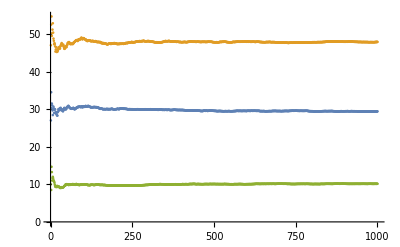

```mathematica
ListPlot[{pt1,pt2,pt3}]
```

```mathematica
(41/50*0.91)/(√(41/50*0.91+17/16846*0.91+6/23654*0.91))//N
```

0.863164

```mathematica
Max[listNP]
```

0.825837

```mathematica
fracList=calcFrac[listSM,listRR,listNP,0.4,0.8,400];
Transpose[fracList]
```

{{0.0515247,0.0525188,0.0533188,0.0543237,0.0550562,0.0562572,0.0568445,0.0580569,0.059322,0.0601966,0.06125,0.0624204,0.0633894,0.0646438,0.0654206,0.0665761,0.0672154,0.0687237,0.0698006,0.0707071,0.0716374,0.0731343,0.0741301,0.0758514,0.0769231,0.0780255,0.078905,0.0809917,0.0827703,0.0839041,0.0855148,0.0875,0.0884477,0.0897436,0.090573,0.0912477,0.0919325,0.0933333,0.0942308,0.0951456,0.0966469,0.0983936,0.0997963,0.10124,0.10251,0.103814,0.105603,0.106754,0.10793,0.10962,0.11036,0.111617,0.113953,0.116667,0.117788,0.119804,0.118812,0.119701,0.122449,0.123393,0.125,0.12766,0.12973,0.132964,0.136364,0.139942,0.141176,0.145015,0.146417,0.146965,0.149351,0.15082,0.153846,0.159722,0.162544,0.166065,0.168498,0.171642,0.174242,0.176245,0.176245,0.179688,0.183267,0.188525,0.193277,0.194915,0.195745,0.2,0.204545,0.208333,0.212264,0.211538,0.21256,0.21393,0.219388,0.225131,0.229947,0.236264,0.242938,0.25,0.255952,0.260606,0.263804,0.265432,0.27044,0.275641,0.282895,0.284768,0.284768,0.287671,0.291667,0.291667,0.297872,0.3,0.302158,0.304348,0.308824,0.313433,0.310606,0.312977,0.322835,0.325397,0.330645,0.333333,0.341667,0.347458,0.356522,0.359649,0.366071,0.366071,0.369369,0.372727,0.376147,0.37963,0.37963,0.383178,0.386792,0.390476,0.390476,0.401961,0.393939,0.393939,0.397959,0.40625,0.410526,0.414894,0.423913,0.428571,0.433333,0.438202,0.431818,0.431818,0.436782,0.44186,0.457831,0.45679,0.468354,0.468354,0.474359,0.486842,0.486842,0.486842,0.493333,0.5,0.492958,0.5,0.492754,0.5,0.515152,0.515152,0.523077,0.523077,0.53125,0.53125,0.52381,0.52459,0.542373,0.561404,0.561404,0.561404,0.561404,0.561404,0.561404,0.571429,0.581818,0.581818,0.592593,0.615385,0.615385,0.627451,0.64,0.64,0.632653,0.632653,0.632653,0.659574,0.659574,0.659574,0.659574,0.666667,0.666667,0.697674,0.714286,0.714286,0.714286,0.707317,0.725,0.725,0.725,0.725,0.736842,0.736842,0.736842,0.736842,0.756757,0.756757,0.777778,0.777778,0.771429,0.764706,0.787879,0.787879,0.787879,0.787879,0.787879,0.78125,0.78125,0.827586,0.857143,0.888889,0.888889,0.884615,0.884615,0.88,0.875,0.875,0.875,0.869565,0.869565,0.869565,0.869565,0.869565,0.909091,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.9,0.894737,0.894737,0.894737,0.944444,0.941176,0.9375,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.928571,0.928571,0.928571,0.928571,0.928571,0.923077,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.9,0.9,0.9,0.9,0.9,0.888889,0.888889,0.888889,0.875,0.875,0.875,0.875,0.875,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.258675,0.258307,0.257889,0.254989,0.255056,0.253731,0.25522,0.251185,0.251816,0.250614,0.25375,0.253503,0.25097,0.251979,0.252336,0.254076,0.255144,0.255259,0.25641,0.252525,0.252924,0.252239,0.248109,0.243034,0.243328,0.243631,0.243156,0.244628,0.239865,0.236301,0.233857,0.232143,0.232852,0.236264,0.238447,0.240223,0.242026,0.238095,0.240385,0.240777,0.244576,0.24498,0.244399,0.243802,0.24477,0.243644,0.241379,0.237473,0.235683,0.237136,0.236486,0.23918,0.244186,0.242857,0.242788,0.239609,0.240099,0.239401,0.239796,0.239075,0.242188,0.239362,0.240541,0.238227,0.241477,0.244898,0.247059,0.250755,0.252336,0.246006,0.25,0.252459,0.257525,0.263889,0.265018,0.267148,0.263736,0.268657,0.265152,0.268199,0.268199,0.273438,0.278884,0.278689,0.277311,0.279661,0.280851,0.284444,0.290909,0.291667,0.292453,0.293269,0.294686,0.298507,0.306122,0.314136,0.315508,0.324176,0.333333,0.331395,0.339286,0.345455,0.349693,0.351852,0.352201,0.358974,0.368421,0.370861,0.370861,0.363014,0.361111,0.361111,0.361702,0.364286,0.366906,0.369565,0.375,0.365672,0.363636,0.358779,0.354331,0.357143,0.362903,0.365854,0.375,0.381356,0.382609,0.385965,0.392857,0.392857,0.396396,0.4,0.40367,0.407407,0.407407,0.411215,0.415094,0.419048,0.419048,0.421569,0.414141,0.414141,0.418367,0.427083,0.431579,0.43617,0.445652,0.450549,0.455556,0.449438,0.443182,0.443182,0.448276,0.453488,0.46988,0.469136,0.481013,0.481013,0.487179,0.5,0.5,0.5,0.506667,0.513889,0.507042,0.514286,0.507246,0.514706,0.530303,0.530303,0.523077,0.523077,0.53125,0.53125,0.52381,0.52459,0.542373,0.561404,0.561404,0.561404,0.561404,0.561404,0.561404,0.571429,0.581818,0.581818,0.592593,0.615385,0.615385,0.627451,0.64,0.64,0.632653,0.632653,0.632653,0.659574,0.659574,0.659574,0.659574,0.666667,0.666667,0.697674,0.714286,0.714286,0.714286,0.707317,0.725,0.725,0.725,0.725,0.736842,0.736842,0.736842,0.736842,0.756757,0.756757,0.777778,0.777778,0.771429,0.764706,0.787879,0.787879,0.787879,0.787879,0.787879,0.78125,0.78125,0.827586,0.857143,0.888889,0.888889,0.884615,0.884615,0.88,0.875,0.875,0.875,0.869565,0.869565,0.869565,0.869565,0.869565,0.909091,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.904762,0.9,0.894737,0.894737,0.894737,0.944444,0.941176,0.9375,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.928571,0.928571,0.928571,0.928571,0.928571,0.923077,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.909091,0.9,0.9,0.9,0.9,0.9,0.888889,0.888889,0.888889,0.875,0.875,0.875,0.875,0.875,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.857143,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

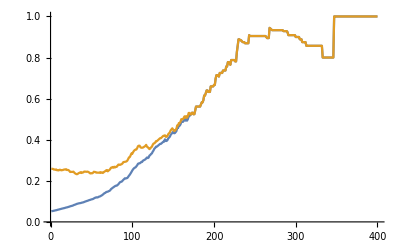

```mathematica
ListLinePlot[Transpose[fracList]]
```

## Compare ESS

```mathematica
essdata=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\essdatav0.csv","CSV"]];
```

```mathematica
Length[listSM]
```

16846

```mathematica
type1AA=0;
type1BA=0;
type1AB=0;
type2AA=0;
type2BA=0;
type2AB=0;
type3AA=0;
type3BA=0;
type3AB=0;
For[i=1,i≤Length[essdata],i++,
If[i≤16846,
If[1==essdata[[i,2]],
If[listSM[[i]]>0.617,type1AA=type1AA+1,type1AB=type1AB+1],
If[listSM[[i]]>0.617,type1BA=type1BA+1]],
If[i<=40500,
If[1==essdata[[i,2]],
If[listRR[[i-16846]]>0.617,type2AA=type2AA+1,type2AB=type2AB+1],
If[listRR[[i-16846]]>0.617,type2BA=type2BA+1]]
,
If[1==essdata[[i,2]],
If[listNP[[i-40500]]>0.617,type3AA=type3AA+1,type3AB=type3AB+1],
If[listNP[[i-40500]]>0.617,type3BA=type3BA+1]]
]
];
]
type1AA
type1BA
type1AB
type2AA
type2BA
type2AB
type3AA
type3BA
type3AB
```

2

6

15

0

0

6

24

4

17

```mathematica
Sum[If[listSM[[n]]>0.617,1,0],{n,1,Length[listSM]}]
```

8

```mathematica
Sum[If[listRR[[n]]>0.617,1,0],{n,1,Length[listRR]}]
```

0

```mathematica
Sum[If[listNP[[n]]>0.617,1,0],{n,1,Length[listNP]}]
```

28

```mathematica
Length[listSM]
```

16846

```mathematica
((24+17)/50*0.91)/(√((24+17)/50*0.91+(2+15)/16846*306.6+6/23654*430.5))//N
```

0.6914

```mathematica
((24+4)/50*0.91)/(√((24+4)/50*0.91+(2+6)/16846*306.6+0/23654*430.5))//N
```

0.629567

```mathematica
essdata[[40501]]
```

{2,1}

```mathematica
16846+23654
```

40500

```mathematica
listNP[[1]]
```

0.70647

## Constraint

```mathematica
HistoryData=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0.csv","CSV"]];
HistoryData2=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv0-1.csv","CSV"]];
res01=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n0-1.csv","CSV"]];
res02=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n0-2.csv","CSV"]];
res03=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n0-3.csv","CSV"]];
res04=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n0-4.csv","CSV"]];
res05=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n0-5.csv","CSV"]];
res1=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n1.csv","CSV"]];
res2=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n2.csv","CSV"]];
res3=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n3.csv","CSV"]];
res4=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-n4.csv","CSV"]];
```

```mathematica
res01[[1]]
```

{0.,27.955}

```mathematica
listSM0={};
listRR0={};
listNP0={};
ProgressIndicator[Dynamic[prog]]
prog=0;
progstep=N[1/(Length[HistoryData]+Length[HistoryData]+Length[HistoryData]+Length[HistoryData]+Length[HistoryData])];
cn0=N[2HarmonicNumber[Length[res01]-1]-2(Length[res01]-1)/Length[res01]];
For[i=1,i<=Length[res01],i++,
If[Round[res01[[i,1]]]==0,AppendTo[listSM0,scorelst[{res01[[i,2]],res02[[i,2]],res03[[i,2]],res04[[i,2]],res05[[i,2]]},cn0]]];
If[Round[res01[[i,1]]]==1,AppendTo[listRR0,scorelst[{res01[[i,2]],res02[[i,2]],res03[[i,2]],res04[[i,2]],res05[[i,2]]},cn0]]];
If[Round[res01[[i,1]]]==2,AppendTo[listNP0,scorelst[{res01[[i,2]],res02[[i,2]],res03[[i,2]],res04[[i,2]],res05[[i,2]]},cn0]]];

prog=prog+progstep;
]
listSM10={};
listRR10={};
listNP10={};
cn1=N[2HarmonicNumber[Length[res1]-1]-2(Length[res1]-1)/Length[res1]];
For[i=1,i<=Length[res1],i++,
If[Round[res1[[i,1]]]==0,AppendTo[listSM10,scorefast[res1[[i,2]],cn1]]];
If[Round[res1[[i,1]]]==1,AppendTo[listRR10,scorefast[res1[[i,2]],cn1]]];
If[Round[res1[[i,1]]]==2,AppendTo[listNP10,scorefast[res1[[i,2]],cn1]]];

prog=prog+progstep;
]
listSM20={};
listRR20={};
listNP20={};
cn2=N[2HarmonicNumber[Length[res2]-1]-2(Length[res2]-1)/Length[res2]];
For[i=1,i<=Length[res2],i++,
If[Round[res2[[i,1]]]==0,AppendTo[listSM20,scorefast[res2[[i,2]],cn2]]];
If[Round[res2[[i,1]]]==1,AppendTo[listRR20,scorefast[res2[[i,2]],cn2]]];
If[Round[res2[[i,1]]]==2,AppendTo[listNP20,scorefast[res2[[i,2]],cn2]]];

prog=prog+progstep;
]
listSM30={};
listRR30={};
listNP30={};
cn3=N[2HarmonicNumber[Length[res3]-1]-2(Length[res3]-1)/Length[res3]];
For[i=1,i<=Length[res3],i++,
If[Round[res3[[i,1]]]==0,AppendTo[listSM30,scorefast[res3[[i,2]],cn3]]];
If[Round[res3[[i,1]]]==1,AppendTo[listRR30,scorefast[res3[[i,2]],cn3]]];
If[Round[res3[[i,1]]]==2,AppendTo[listNP30,scorefast[res3[[i,2]],cn3]]];

prog=prog+progstep;
]
listSM40={};
listRR40={};
listNP40={};
cn4=N[2HarmonicNumber[Length[res4]-1]-2(Length[res4]-1)/Length[res4]];
For[i=1,i<=Length[res4],i++,
If[Round[res4[[i,1]]]==0,AppendTo[listSM40,scorefast[res4[[i,2]],cn4]]];
If[Round[res4[[i,1]]]==1,AppendTo[listRR40,scorefast[res4[[i,2]],cn4]]];
If[Round[res4[[i,1]]]==2,AppendTo[listNP40,scorefast[res4[[i,2]],cn4]]];

prog=prog+progstep;
]
listSM50={};
listRR50={};
listNP50={};
maxl=1001;
cn5=N[2HarmonicNumber[Length[HistoryData]-1]-2(Length[HistoryData]-1)/Length[HistoryData]];
For[i=1,i<=Length[HistoryData],i++,
If[Round[HistoryData[[i,1]]]==0,AppendTo[listSM50,scorelst[{Mean[Take[HistoryData[[i]],{2,maxl}]],Mean[Take[HistoryData2[[i]],{2,maxl}]]},cn5]]];
If[Round[HistoryData[[i,1]]]==1,AppendTo[listRR50,scorelst[{Mean[Take[HistoryData[[i]],{2,maxl}]],Mean[Take[HistoryData2[[i]],{2,maxl}]]},cn5]]];
If[Round[HistoryData[[i,1]]]==2,AppendTo[listNP50,scorelst[{Mean[Take[HistoryData[[i]],{2,maxl}]],Mean[Take[HistoryData2[[i]],{2,maxl}]]},cn5]]];

prog=prog+progstep;
]
```

```mathematica
Min[listSM0-listSM50]
```

0.00224183

```mathematica
Max[listSM0-listSM50]
```

0.0749968

```mathematica
BinCounts[listSM0-listSM50,{0,0.075,0.0025}]
```

{1,138,1649,3991,4033,2581,1675,988,649,370,271,147,111,69,49,41,22,21,13,7,4,6,5,0,2,1,0,0,1,1}

```mathematica
Min[listRR0-listRR50]
```

0.00128717

```mathematica
Max[listRR0-listRR50]
```

0.0511713

```mathematica
BinCounts[listRR0-listRR50,{0,0.075,0.0025}]
```

{8,285,2942,7188,6441,3446,1660,847,394,196,113,43,36,18,14,17,3,1,0,0,2,0,0,0,0,0,0,0,0,0}

```mathematica
amin=0.63;
```

```mathematica
lscs={(Sum[If[listSM0[[n]]>amin,1,0],{n,1,Length[listSM0]}]+Sum[If[listNP0[[n]]>amin,1,0],{n,1,Length[listNP0]}])*306.6/16846,
(Sum[If[listSM10[[n]]>amin,1,0],{n,1,Length[listSM10]}]+Sum[If[listNP10[[n]]>amin,1,0],{n,1,Length[listNP10]}])*306.6/16846,
(Sum[If[listSM20[[n]]>amin,1,0],{n,1,Length[listSM20]}]+Sum[If[listNP20[[n]]>amin,1,0],{n,1,Length[listNP20]}])*306.6/16846,
(Sum[If[listSM30[[n]]>amin,1,0],{n,1,Length[listSM30]}]+Sum[If[listNP30[[n]]>amin,1,0],{n,1,Length[listNP30]}])*306.6/16846,
(Sum[If[listSM40[[n]]>amin,1,0],{n,1,Length[listSM40]}]+Sum[If[listNP40[[n]]>amin,1,0],{n,1,Length[listNP40]}])*306.6/16846,
(Sum[If[listSM50[[n]]>amin,1,0],{n,1,Length[listSM50]}]+Sum[If[listNP50[[n]]>amin,1,0],{n,1,Length[listNP50]}])*306.6/16846}
```

{0.327603,0.382203,0.418604,0.455004,0.491404,0.491404}

```mathematica
√137.1(lscs-lscs[[1]])/(√lscs)
```

{0.,1.48929,2.1193,2.69423,2.69423,2.96439}

```mathematica
0.013*{0,√(1/5),√(2/5),√(3/5),√(4/5),1}
```

{0.,0.00581378,0.00822192,0.0100698,0.0116276,0.013}

```mathematica
amin=0.66;
```

```mathematica
Sum[If[listRR0[[n]]>amin,1,0],{n,1,Length[listRR0]}]
Sum[If[listRR10[[n]]>amin,1,0],{n,1,Length[listRR10]}]
Sum[If[listRR20[[n]]>amin,1,0],{n,1,Length[listRR20]}]
Sum[If[listRR30[[n]]>amin,1,0],{n,1,Length[listRR30]}]
Sum[If[listRR40[[n]]>amin,1,0],{n,1,Length[listRR40]}]
Sum[If[listRR50[[n]]>amin,1,0],{n,1,Length[listRR50]}]
```

0

0

0

«3 more identical outputs»

```mathematica
Sum[If[listNP0[[n]]>0.65,1,0],{n,1,Length[listNP0]}]
Sum[If[listNP10[[n]]>0.65,1,0],{n,1,Length[listNP10]}]
Sum[If[listNP20[[n]]>0.65,1,0],{n,1,Length[listNP20]}]
Sum[If[listNP30[[n]]>0.65,1,0],{n,1,Length[listNP30]}]
Sum[If[listNP40[[n]]>0.65,1,0],{n,1,Length[listNP40]}]
Sum[If[listNP50[[n]]>0.65,1,0],{n,1,Length[listNP50]}]
```

0

6

11

14

16

19

## V3 Results

```mathematica
h1=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv3.csv","CSV"]];
h2=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv3-1.csv","CSV"]];
h3=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv3-2.csv","CSV"]];
h4=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\historyv3-3.csv","CSV"]];
```

```mathematica
listSM={};
listRR={};
listNP={};
maxl=501;
ProgressIndicator[Dynamic[prog]]
prog=0;
cn=N[2HarmonicNumber[Length[h1]-1]-2(Length[h1]-1)/Length[h1]];
For[i=1,i<=Length[h1],i++,
If[Round[h1[[i,1]]]==0,AppendTo[listSM,scorelst[{Mean[Take[h1[[i]],{2,maxl}]],Mean[Take[h2[[i]],{2,maxl}]],Mean[Take[h3[[i]],{2,maxl}]],Mean[Take[h4[[i]],{2,maxl}]]},cn]]];
If[Round[h1[[i,1]]]==1,AppendTo[listRR,scorelst[{Mean[Take[h1[[i]],{2,maxl}]],Mean[Take[h2[[i]],{2,maxl}]],Mean[Take[h3[[i]],{2,maxl}]],Mean[Take[h4[[i]],{2,maxl}]]},cn]]];
If[Round[h1[[i,1]]]==2,AppendTo[listNP,scorelst[{Mean[Take[h1[[i]],{2,maxl}]],Mean[Take[h2[[i]],{2,maxl}]],Mean[Take[h3[[i]],{2,maxl}]],Mean[Take[h4[[i]],{2,maxl}]]},cn]]];
prog=prog+N[1/Length[h1]];
]
```

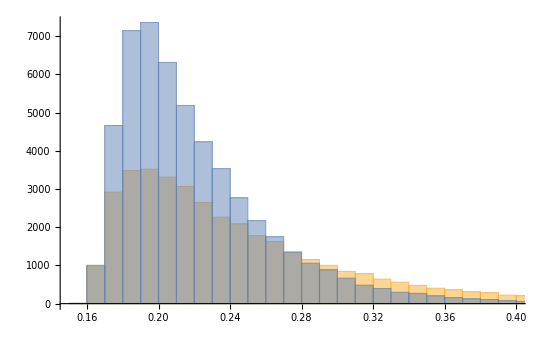

```mathematica
Histogram[{listSM,listRR},50]
```

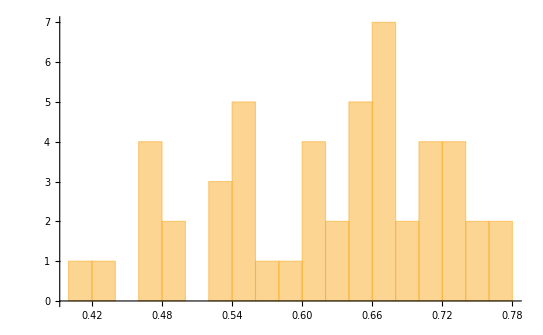

```mathematica
Histogram[{listNP},12]
```

```mathematica
calcBins[listNP,0.1,0.8,35]
calcBins[listSM,0.1,0.8,35]
calcBins[listRR,0.1,0.8,35]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,4,2,0,3,5,1,1,4,2,5,7,2,4,4,2,2,0}

{0,0,10,3906,7003,6382,4911,3864,2986,2157,1628,1209,883,673,507,376,226,218,161,90,52,49,33,25,16,8,11,3,2,0,0,1,0,0,0}

{0,0,11,5666,14501,11499,7765,4942,3088,1941,1155,695,470,283,184,121,64,48,27,20,10,4,4,2,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
calcSS[listSM,listRR,listNP,0.414/50,0.414/50,0.414/50,0.5,500]
```

{0.23611,0.237016,0.237473,0.238861,0.24171,0.243667,0.244664,0.24721,0.248776,0.249305,0.250372,0.25366,0.2565,0.258251,0.260038,0.261251,0.264357,0.264992,0.267577,0.268899,0.27024,0.265807,0.267166,0.264057,0.264755,0.26906,0.270543,0.27205,0.273583,0.274359,0.277531,0.279983,0.281655,0.283357,0.28775,0.282326,0.286902,0.291708,0.291708,0.2937,0.295732,0.295732,0.297807,0.298862,0.301004,0.304306,0.308882,0.308882,0.311249,0.313671,0.317413,0.314345,0.315652,0.31126,0.315329,0.300936,0.303659,0.29909,0.300498,0.304842,0.306333,0.31094,0.31094,0.317419,0.319102,0.320813,0.32432,0.329802,0.331692,0.331692,0.335571,0.33959,0.33959,0.341655,0.341655,0.343757,0.350305,0.352573,0.354885,0.346736,0.349071,0.349071,0.353886,0.358905,0.364145,0.366853,0.366853,0.369621,0.372454,0.369802,0.375915,0.379087,0.379087,0.379087,0.379087,0.379087,0.385681,0.385681,0.385681,0.385681,0.385681,0.389109,0.39263,0.396249,0.396249,0.403797,0.407737,0.411794,0.411794,0.411794,0.411794,0.402976,0.402976,0.389076,0.389076,0.389076,0.37981,0.37981,0.37981,0.37981,0.37981,0.37981,0.384102,0.388543,0.393141,0.393141,0.393141,0.383696,0.393411,0.398554,0.403904,0.39431,0.399903,0.405741,0.405741,0.405741,0.405741,0.411843,0.411843,0.411843,0.418228,0.418228,0.42492,0.415331,0.415331,0.415331,0.415331,0.415331,0.415331,0.405534,0.402774,0.402774,0.400376,0.400376,0.400376,0.390058,0.390058,0.390058,0.390058,0.390058,0.390058,0.390058,0.390058,0.390058,0.398447,0.398447,0.398447,0.388002,0.388002,0.388002,0.377276,0.377276,0.386593,0.386593,0.37576,0.353111,0.353111,0.341229,0.341229,0.341229,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.328926,0.316151,0.302848,0.302848,0.302848,0.302848,0.302848,0.302848,0.302848,0.288946,0.288946,0.288946,0.288946,0.288946,0.288946,0.288946,0.274359,0.258975,0.258975,0.258975,0.258975,0.258975,0.258975,0.258975,0.258975,0.258975,0.242652,0.242652,0.242652,0.242652,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.2252,0.240749,0.240749,0.240749,0.240749,0.240749,0.240749,0.22289,0.22289,0.20347,0.181989,0.181989,0.181989,0.157607,0.157607,0.157607,0.157607,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0.128686,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
0.4249
```

```mathematica
0.297/(√(0.297`+0.29+1.74*0.23*0.23))
```

0.476163

```mathematica
(35/50*0.41)/(√(35/50*0.41+40/37390*0.41+13/52500*0.41))//N
```

0.53522

```mathematica
fracListv3=calcFrac[listSM,listRR,listNP,0.4,0.75,350];
Transpose[fracListv3]
```

{{0.0308452,0.0315657,0.0319285,0.0325521,0.0330251,0.0329744,0.0334699,0.0340988,0.0348011,0.0354302,0.0362158,0.0369811,0.0379257,0.0387046,0.0393258,0.0400654,0.0407315,0.0412805,0.0419162,0.0425347,0.0436331,0.0444646,0.0450368,0.0456664,0.0464455,0.0468004,0.0478049,0.0483712,0.0489022,0.049545,0.050308,0.0507246,0.0512552,0.0521832,0.053203,0.0539648,0.0550562,0.0557452,0.0566474,0.057377,0.0576923,0.0583232,0.06,0.0606061,0.0615385,0.0621762,0.0635762,0.0649526,0.066482,0.0673212,0.0692641,0.0702782,0.0711111,0.0733945,0.0751174,0.0766773,0.0777958,0.0790774,0.0808081,0.0833333,0.0848057,0.0864865,0.0863971,0.0878505,0.0898662,0.0907336,0.0928854,0.0909091,0.0929752,0.09375,0.0965665,0.0986842,0.100446,0.10274,0.105882,0.106888,0.109223,0.1125,0.113402,0.114883,0.117647,0.120219,0.119444,0.120787,0.123209,0.124638,0.126471,0.128743,0.128049,0.12963,0.135484,0.139073,0.141892,0.145833,0.147368,0.15,0.152174,0.154412,0.155556,0.156716,0.160305,0.161538,0.162162,0.164063,0.168,0.170732,0.172131,0.175732,0.177966,0.178723,0.180258,0.185022,0.189189,0.191781,0.194444,0.196262,0.200957,0.201923,0.205882,0.207921,0.21,0.208122,0.210256,0.210526,0.21164,0.218579,0.220994,0.223464,0.225989,0.227273,0.232558,0.236686,0.239521,0.242424,0.25,0.246835,0.254902,0.263514,0.263514,0.267123,0.270833,0.270833,0.274648,0.276596,0.280576,0.286765,0.295455,0.295455,0.3,0.304688,0.312,0.31405,0.316667,0.316239,0.324561,0.3125,0.318182,0.317757,0.320755,0.330097,0.333333,0.343434,0.343434,0.357895,0.361702,0.365591,0.373626,0.386364,0.390805,0.390805,0.4,0.409639,0.409639,0.414634,0.414634,0.419753,0.435897,0.441558,0.447368,0.44,0.445946,0.445946,0.458333,0.471429,0.485294,0.492537,0.492537,0.5,0.507692,0.516129,0.533333,0.542373,0.542373,0.542373,0.542373,0.542373,0.561404,0.561404,0.561404,0.561404,0.561404,0.571429,0.581818,0.592593,0.592593,0.615385,0.627451,0.64,0.64,0.64,0.64,0.632653,0.632653,0.630435,0.630435,0.630435,0.622222,0.622222,0.622222,0.622222,0.622222,0.622222,0.636364,0.651163,0.666667,0.666667,0.666667,0.658537,0.692308,0.710526,0.72973,0.722222,0.742857,0.764706,0.764706,0.764706,0.764706,0.787879,0.787879,0.787879,0.8125,0.8125,0.83871,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.827586,0.851852,0.851852,0.88,0.88,0.88,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.913043,0.913043,0.913043,0.909091,0.909091,0.909091,0.904762,0.904762,0.95,0.95,0.947368,0.941176,0.941176,0.9375,0.9375,0.9375,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.928571,0.923077,0.923077,0.923077,0.923077,0.923077,0.923077,0.923077,0.916667,0.916667,0.916667,0.916667,0.916667,0.916667,0.916667,0.909091,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.888889,0.888889,0.888889,0.888889,0.875,0.875,0.875,0.875,0.875,0.875,0.875,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{0.215916,0.21654,0.215837,0.218099,0.217966,0.217362,0.217896,0.219207,0.215909,0.214027,0.214339,0.215849,0.214396,0.21327,0.211878,0.209321,0.20532,0.203875,0.204448,0.203993,0.203028,0.200544,0.200368,0.203169,0.201896,0.201528,0.202927,0.204344,0.204591,0.204247,0.205339,0.207039,0.200837,0.200213,0.198697,0.200441,0.2,0.197952,0.196532,0.194379,0.195913,0.193196,0.19625,0.19697,0.198718,0.198187,0.198675,0.194858,0.196676,0.194951,0.194805,0.194729,0.195556,0.197248,0.198748,0.196486,0.197731,0.199341,0.200337,0.203125,0.20318,0.207207,0.209559,0.211215,0.210325,0.208494,0.211462,0.20404,0.206612,0.208333,0.203863,0.20614,0.207589,0.210046,0.216471,0.218527,0.223301,0.225,0.224227,0.224543,0.224599,0.221311,0.219444,0.219101,0.223496,0.223188,0.223529,0.227545,0.222561,0.225309,0.225806,0.225166,0.226351,0.225694,0.22807,0.228571,0.231884,0.235294,0.237037,0.238806,0.236641,0.234615,0.235521,0.238281,0.24,0.239837,0.241803,0.246862,0.25,0.251064,0.244635,0.246696,0.247748,0.251142,0.25463,0.257009,0.258373,0.254808,0.259804,0.262376,0.26,0.258883,0.261538,0.263158,0.26455,0.26776,0.270718,0.268156,0.271186,0.272727,0.27907,0.278107,0.281437,0.284848,0.29375,0.291139,0.294118,0.304054,0.304054,0.308219,0.3125,0.3125,0.309859,0.304965,0.309353,0.316176,0.325758,0.325758,0.330769,0.335938,0.336,0.338843,0.341667,0.333333,0.342105,0.330357,0.336364,0.336449,0.339623,0.349515,0.352941,0.363636,0.363636,0.378947,0.382979,0.387097,0.395604,0.409091,0.402299,0.402299,0.411765,0.421687,0.421687,0.426829,0.426829,0.432099,0.435897,0.441558,0.447368,0.44,0.445946,0.445946,0.458333,0.471429,0.485294,0.492537,0.492537,0.5,0.507692,0.516129,0.533333,0.542373,0.542373,0.542373,0.542373,0.542373,0.561404,0.561404,0.561404,0.561404,0.561404,0.571429,0.581818,0.592593,0.592593,0.615385,0.627451,0.64,0.64,0.64,0.64,0.632653,0.632653,0.630435,0.630435,0.630435,0.622222,0.622222,0.622222,0.622222,0.622222,0.622222,0.636364,0.651163,0.666667,0.666667,0.666667,0.658537,0.692308,0.710526,0.72973,0.722222,0.742857,0.764706,0.764706,0.764706,0.764706,0.787879,0.787879,0.787879,0.8125,0.8125,0.83871,0.833333,0.833333,0.833333,0.833333,0.833333,0.833333,0.827586,0.851852,0.851852,0.88,0.88,0.88,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.875,0.913043,0.913043,0.913043,0.909091,0.909091,0.909091,0.904762,0.904762,0.95,0.95,0.947368,0.941176,0.941176,0.9375,0.9375,0.9375,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.933333,0.928571,0.923077,0.923077,0.923077,0.923077,0.923077,0.923077,0.923077,0.916667,0.916667,0.916667,0.916667,0.916667,0.916667,0.916667,0.909091,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.9,0.888889,0.888889,0.888889,0.888889,0.875,0.875,0.875,0.875,0.875,0.875,0.875,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

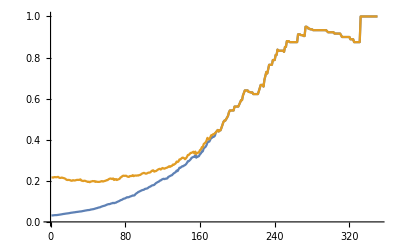

```mathematica
ListLinePlot[Transpose[fracListv3]]
```

```mathematica
essdata=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\essdatav3.csv","CSV"]];
```

```mathematica
type1AA=0;
type1BA=0;
type1AB=0;
type2AA=0;
type2BA=0;
type2AB=0;
type3AA=0;
type3BA=0;
type3AB=0;
For[i=1,i≤Length[essdata],i++,
If[i≤37390,
If[1==essdata[[i,2]],
If[listSM[[i]]>0.642,type1AA=type1AA+1,type1AB=type1AB+1],
If[listSM[[i]]>0.642,type1BA=type1BA+1]],
If[i≤89890,
If[1==essdata[[i,2]],
If[listRR[[i-37390]]>0.642,type2AA=type2AA+1,type2AB=type2AB+1],
If[listRR[[i-37390]]>0.642,type2BA=type2BA+1]]
,
If[1==essdata[[i,2]],
If[listNP[[i-89890]]>0.642,type3AA=type3AA+1,type3AB=type3AB+1],
If[listNP[[i-89890]]>0.642,type3BA=type3BA+1]]
]
];
]
type1AA
type1BA
type1AB
type2AA
type2BA
type2AB
type3AA
type3BA
type3AB
```

0

5

37

0

0

12

17

9

17

```mathematica
((17+9)/50*0.414)/(√((17+9)/50*0.414+(0+5)/37390*306.6+0/52500*430.5))//N
```

0.425252

```mathematica
((17+17)/50*0.414)/(√((17+17)/50*0.414+(0+37)/37390*306.6+12/52500*430.5))//N
```

0.340562

## 3 D Data

```mathematica
ToExpression["p_{\ell^+}\cdot p_{\ell^-}",TeXForm,HoldForm]
```

p_(ℓ^+)·p_(ℓ^-)

```mathematica
dataSets1=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\v0event2d.csv","CSV"]];
```

```mathematica
listSM={};
listRR={};
listNP={};
ProgressIndicator[Dynamic[prog]]
prog=0;
For[i=1,i<=Length[dataSets1],i++,
If[Round[dataSets1[[i,3]]]==0,AppendTo[listSM,{dataSets1[[i,1]],dataSets1[[i,2]]}]];
If[Round[dataSets1[[i,3]]]==1,AppendTo[listRR,{dataSets1[[i,1]],dataSets1[[i,2]]}]];
If[Round[dataSets1[[i,3]]]==2,AppendTo[listNP,{dataSets1[[i,1]],dataSets1[[i,2]]}]];
prog=prog+N[1/Length[dataSets1]];
]
```

```mathematica
Histogram3D[{listSM,listRR,listNP},50,ChartLayout->"Stacked",ChartBaseStyle->Opacity[1],TicksStyle->Directive[Black,20],ChartStyle->{Red,Green,Blue}]
```

-Graphics3D-

```mathematica
b1=Table[Exp[0.251x],{x,-1,30}]//N
b2=Table[Exp[0.558x],{x,-1,30}]//N
```

{0.778022,1.,1.28531,1.65202,2.12336,2.72918,3.50784,4.50866,5.79503,7.44841,9.57351,12.3049,15.8157,20.328,26.1278,33.5823,43.1637,55.4787,71.3074,91.6521,117.801,151.411,194.61,250.135,321.501,413.228,531.126,682.662,877.432,1127.77,1449.54,1863.11}

{0.572353,1.,1.74717,3.05262,5.33346,9.31848,16.281,28.4458,49.6998,86.8342,151.714,265.072,463.126,809.163,1413.75,2470.07,4315.64,7540.17,13174.,23017.3,40215.2,70263.,122762.,214486.,374745.,654744.,1.14395×10^6,1.99868×10^6,3.49205×10^6,6.10122×10^6,1.06599×10^7,1.86247×10^7}

```mathematica
Max[Table[listNP[[n,2]],{n,1,Length[listNP]}]]
```

1.82759×10^7

```mathematica
SetOptions[$FrontEndSession,RenderingOptions->{"3DRenderingEngine"->"Direct3D","3DRenderingMethod"->"BSP"}]
```

```mathematica
Histogram3D[{listRR,listSM,listNP},{{b1},{b2}},ScalingFunctions->{"Log","Log","Log"},ChartLayout->"Stacked",TicksStyle->Directive[Black,20],ChartStyle->{Directive[EdgeForm[Green], FaceForm[{Green,Opacity[0.8]}]],Directive[EdgeForm[Red], FaceForm[{Red,Opacity[0.8]}]],Directive[EdgeForm[Blue], FaceForm[{Blue,Opacity[0.8]}]]},PerformanceGoal->"Quality"(*,Method->{"RelieveDPZFighting"->True}*)]/.EdgeForm[___]->Directive[EdgeForm[{Black,AbsoluteThickness[0.0001]}]]
```

-Graphics3D-

```mathematica
dataSet2A=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-2d-0.csv","CSV"]];
dataSet2B=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-2d-1.csv","CSV"]];
dataSet2C=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-2d-2.csv","CSV"]];
dataSet2D=ToExpression[Import["F:\\PyworkingFolder\\CutExperiment\\Applications\\KMeans\\resultv0-2d-3.csv","CSV"]];
```

```mathematica
list7={};
list6={};
listn={};
cn=N[2HarmonicNumber[Length[dataSet2A]-1]-2(Length[dataSet2A]-1)/Length[dataSet2A]];
ProgressIndicator[Dynamic[prog]]
prog=0;
For[i=1,i<=Length[dataSets1],i++,
scoreofthisP=scorefast[(dataSet2A[[i,2]]+dataSet2B[[i,2]]+dataSet2C[[i,2]]+dataSet2D[[i,2]])/4,cn];
If[scoreofthisP> 0.7,AppendTo[list7,{dataSets1[[i,1]],dataSets1[[i,2]]}],
If[scoreofthisP>0.6,AppendTo[list6,{dataSets1[[i,1]],dataSets1[[i,2]]}],
AppendTo[listn,{dataSets1[[i,1]],dataSets1[[i,2]]}]
];
];
prog=prog+N[1/Length[dataSets1]];
]
```

```mathematica
Histogram3D[{listn,list6,list7},50,ChartLayout->"Stacked",ChartBaseStyle->Opacity[1],TicksStyle->Directive[Black,20],ChartStyle->{Red,Green,Blue}]
```

-Graphics3D-

```mathematica
Histogram3D[{listn,list6,list7},{{b1},{b2}},ScalingFunctions->{"Log","Log","Log"},ChartLayout->"Stacked",TicksStyle->Directive[Black,20],ChartStyle->{Directive[EdgeForm[Green], FaceForm[{Green,Opacity[0.7]}]],Directive[EdgeForm[Red], FaceForm[{Red,Opacity[0.7]}]],Directive[EdgeForm[Blue], FaceForm[{Blue,Opacity[0.7]}]]}]/.EdgeForm[___]->Directive[EdgeForm[{Black,AbsoluteThickness[0.001]}]]
```

-Graphics3D-